## SVD Unit Tests

```mathematica
SetDirectory[NotebookDirectory[]];
getTransSVD[ptsSrc_,ptsTgt_]:=Module[{cent1,cent2,matP,matQ,mat,u,w,v,r,func,vec},
(* getting the centroid *)
cent1=Mean[ptsSrc];
cent2=Mean[ptsTgt];

(* forming the cross-covariance matrix *)
matP=Map[(#-cent1)&,ptsSrc];
matQ=Map[(#-cent2)&,ptsTgt];
mat=Transpose[matP].matQ;

(* SVD decomposition *)
{u,w,v}=SingularValueDecomposition[mat];

(* obtaining the rotation *)
r=v.Transpose[u];
vec=cent2-cent1;
(* transform *)
func[pts_]:=Module[{npts,nmat,ncent},
ncent=Mean[pts];(*I think this line is a bug. I believe that this is corrected with the following line.*)
ncent=cent1;
nmat=Map[(#-ncent)&,pts];
npts=Transpose[r.Transpose[nmat]];
Map[(#+vec+ncent)&,npts]];

func];
```

```mathematica
(*Generate random points to test on in c++*)
RandomSeed[0];
randReal [e_]:=RandomReal[{-e,e}];
perturb[pts_,e_]:=Map[(Map[(#+RandomReal[{-e,e}])&,#])&,pts];
genSVDTest [n_]:=Module[{alignSource, alignTarget, mapSource, mapTest, randVec}, 
alignSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[5]]//N;
randVec = {randReal[100], randReal[100]};
(*Rotate, then translate, then add random noise*)
alignTarget = perturb[Map[(#+randVec)&,Transpose[RotationMatrix[randReal[π]].Transpose[alignSource]]], randReal[10]]//N;
mapSource = Map[(Map[(RandomReal[{-100,100}])&,Range[2]])&,Range[n]] //N;
 mapTest = getTransSVD[alignSource,alignTarget][mapSource]//N;
{alignSource, alignTarget, mapSource, mapTest}
]
```

```mathematica
(*Generate tests, then export them to the selected file*)
svdTests = Map[(genSVDTest[#*10])&,Range[250]]//N
(*Export["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\UnitTest\\svd.json", svdTests];*)
```

{1}
 |  |  |  |

## Grow and Cover Unit Tests

### Utility Functions

```mathematica
ϵ=0.2;
rotM[a_]:=N[{{Cos[a],-Sin[a]},{Sin[a],Cos[a]}}];
hexM=N[rotM[π/3]];
```

```mathematica
getCoords[pt_,origin_,v1_,v2_]:=Inverse[Transpose[{v1,v2}]].(pt-origin);
getPt[coords_,origin_,v1_,v2_]:=coords.{v1,v2}+origin;
```

### Init Functions

```mathematica
getInliers[pts_,{origin_,vec_}]:=Module[{intcoords,vec2=hexM.vec,inds},
intcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,pts];
inds=Select[Range[Length[pts]],(Norm[pts⟦#⟧-getPt[intcoords⟦#⟧,origin,vec,vec2]]<ϵ*Norm[vec])&];
{inds,intcoords⟦inds⟧}];
```

```mathematica
initGridInliers[pts_,num_]:=Module[{ori,v,in={{},{}},oriTemp,vTemp,inTemp},
Do[oriTemp=RandomSample[pts,1]⟦1⟧;
vTemp=Nearest[pts,oriTemp,2]⟦2⟧-oriTemp;
inTemp=getInliers[pts,{oriTemp,vTemp}];
If[Length[inTemp⟦1⟧]>Length[in⟦1⟧],
ori=oriTemp;
v=vTemp;
in=inTemp],
{i,num}];
{{ori,v},in}];
```

```mathematica
getGrid[pts_,{inds_,intcoords_}]:=Module[{ata=Table[0,{4},{4}],atb=Table[0,{4}],a,I2=IdentityMatrix[2],res},
Do[
a=Transpose[Join[Transpose[intcoords⟦i,1⟧*I2+intcoords⟦i,2⟧*hexM],I2]];
ata+=Transpose[a].a;
atb+=Transpose[a].pts⟦inds⟦i⟧⟧,
{i,Length[inds]}

];
res=Inverse[ata].atb;

(*Origin, V1*)
{res⟦{3,4}⟧,res⟦{1,2}⟧}];
```

```mathematica
refineGrid[pts_,grid_,inliers_]:=Module[{newGrid=grid,newInliers=inliers,num=Length[inliers⟦1⟧]},
While[num<Length[pts],
(* Print["Iterate"]; *)
newGrid=getGrid[pts,newInliers];
newInliers=getInliers[pts,newGrid];
If[Length[newInliers⟦1⟧]>num,
num=Length[newInliers⟦1⟧],
Break[]]];
newGrid=getGrid[pts,newInliers];
{newGrid,newInliers}];
```

```mathematica
getGridAndCoords[pts_,num_]:=Module[{grid,inliers,v2},
{grid,inliers}=initGridInliers[pts,num];
{grid,inliers}=refineGrid[pts,grid,inliers];
v2=hexM.grid⟦2⟧;
{grid,Map[Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]]&,pts]}];
```

### Init Functions Tests (pulls from hexfit.json)

```mathematica
(*Test Function*)
getRangeRatio[pts_,r_]:=Map[{(1-r)Mean[#]+r#⟦1⟧,(1-r)Mean[#]+r#⟦2⟧}&,Transpose[{Map[Min,Transpose[pts]],Map[Max,Transpose[pts]]}]];
drawFit[pts_,{origin_,vec_},intcoords_,ptSize_]:=Module[{r=getRangeRatio[pts,1.2],rcoords,lx,hx,ly,hy,vec2=hexM.vec,inds, outinds},
inds=getInliers[pts,{origin,vec}][[1]];
outinds=Complement[Range[Length[pts]],inds];
rcoords=Map[Round[getCoords[#,origin,vec,vec2]]&,{{r⟦1,1⟧,r⟦2,1⟧},{r⟦1,1⟧,r⟦2,2⟧},{r⟦1,2⟧,r⟦2,1⟧},{r⟦1,2⟧,r⟦2,2⟧}}];
{lx,ly}=Map[Min,Transpose[rcoords]];
{hx,hy}=Map[Max,Transpose[rcoords]];

Graphics[{
{LightGray,Table[Line[{getPt[{x,ly},origin,vec,vec2],getPt[{x,hy},origin,vec,vec2]}],{x,lx,hx}],
Table[Line[{getPt[{lx,y},origin,vec,vec2],getPt[{hx,y},origin,vec,vec2]}],{y,ly,hy}]},
(* calculated grid points *)
{Blue,AbsolutePointSize[ptSize],Map[Point[getPt[#,origin,vec,vec2]]&,intcoords]},
(* outlier points *)
{Red, AbsolutePointSize[ptSize],Map[Point,pts⟦outinds⟧]},
(* inlier points *)
{Green, AbsolutePointSize[ptSize],Map[Point,pts⟦inds⟧]},
(* grid *)
{Black, AbsolutePointSize[ptSize*2],Point[origin]},
{Black,AbsoluteThickness[ptSize],Line[{origin,origin+vec}]}

},
PlotRange->r]];
```

{{{-7.78481,0.0814371},{-0.242362,0.971632}},{{9.00427,1.98054},{0.494866,-0.646639}},{{-2.71391,16.8007},{-0.765892,-0.641409}},{{-6.89487,-5.96073},{0.561557,0.837356}},{{-13.9998,2.77034},{-0.412919,-0.907285}}}

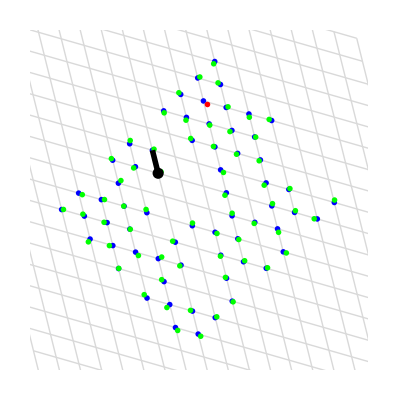
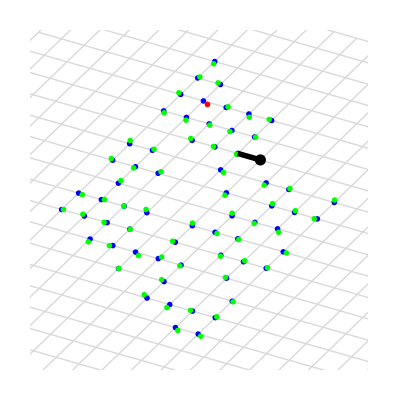
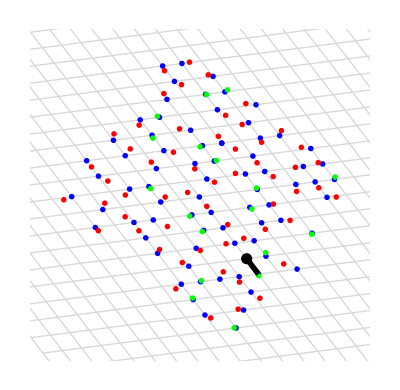
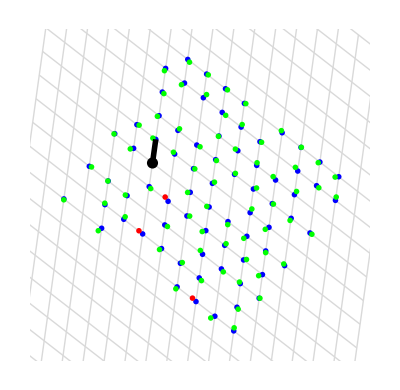
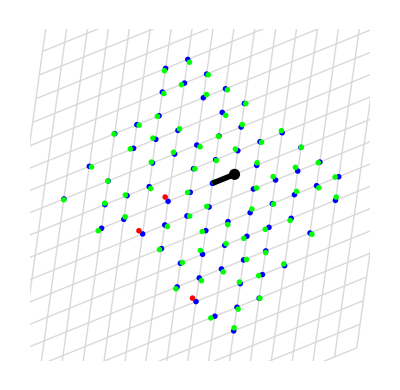
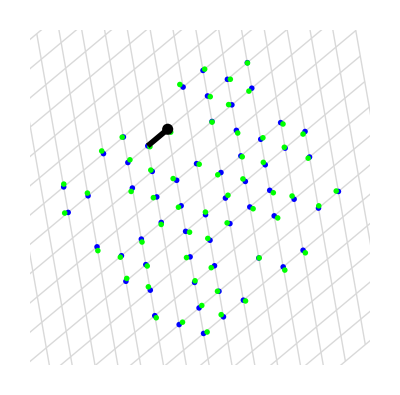
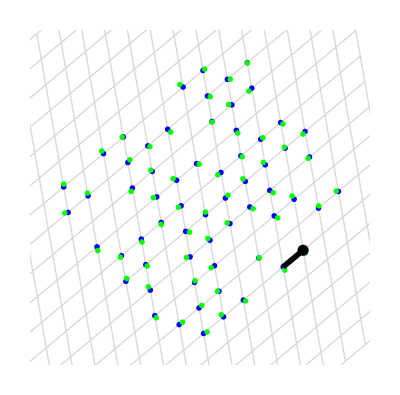
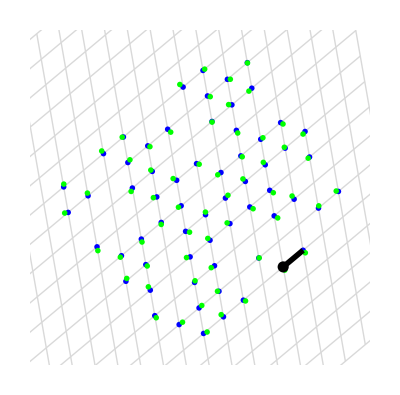
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\hexResults.json"];
importedData[[;;,2]]
importedPlots=Map[(drawFit[#[[1]],#[[2]],#[[3]],4])&,importedData];
mathematicaPlots:=Map[(drawFit[#[[1]],#[[2]][[1]],#[[2]][[2]],4])&,Map[({#[[1]],getGridAndCoords[#[[1]], 50]})&,importedData]];
Column[Transpose[{importedPlots,mathematicaPlots,mathematicaPlots}]]
```

#### RefineGrid Tests (RefineGridMathematica)

```mathematica
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\refineResults.json"];
realInitGrids = Map[(getGrid[#[[1]],getInliers[ #[[1]],#[[2]]]])&,importedData];
newGrids = Map[(refineGrid[#[[1]],#[[2]], getInliers[#[[1]],#[[2]]]][[1]])&,importedData];
MapThread[(#1 - #2[[3]])&,{realInitGrids, importedData}](*getGrid Comparison*)
MapThread[(#1 - #2[[4]])&,{newGrids, importedData}](*refineGrid Comparison*)
```

{{{-8.82914×10^-6,-3.82022×10^-6},{5.95459×10^-7,2.42472×10^-7}},{{1.05395×10^-6,3.50236×10^-7},{9.21714×10^-8,4.15258×10^-8}},{{-2.43247×10^-6,3.85323×10^-7},{1.34323×10^-6,3.62396×10^-7}},{{5.67896×10^-7,5.18815×10^-7},{6.13141×10^-8,5.33977×10^-8}},{{9.04259×10^-6,-2.11829×10^-8},{-1.90718×10^-8,2.08783×10^-6}}}

{{{-2.59173×10^-6,9.55499×10^-7},{9.5049×10^-8,-1.73983×10^-7}},{{-1.14748×10^-6,-1.0365×10^-6},{4.23283×10^-8,-1.296×10^-8}},{{-1.50345×10^-6,-0.0000103483},{-8.76385×10^-7,6.48411×10^-7}},{{-2.58238×10^-7,-5.19253×10^-7},{-1.88553×10^-8,1.96165×10^-7}},{{7.35329×10^-6,2.23876×10^-7},{3.4718×10^-7,-8.3152×10^-7}}}

### The Grow Function

```mathematica
growAndCover[pts_,samples_,wid_,num_]:=Module[{hash,ncoords={},grid,coords,loc,nghbs={{1,0},{0,1},{-1,1},{-1,0},{0,-1},{1,-1}},nghbs2,v2,bd,nbd},
(* Compute grid and coordinates *)
{grid,coords}=getGridAndCoords[pts,num];
Print[grid];
v2=hexM.grid⟦2⟧;

(* Store existing points in hash *)
hash[_,_]=False;
Scan[(hash[#⟦1⟧,#⟦2⟧]=True)&,coords];

(* for each sample, if its nearest grid point and or any of its 6-neighbors are not in the list, add them to the list *)
nghbs2=Append[nghbs,{0,0}];
Scan[
(
loc=Round[getCoords[#,grid⟦1⟧,grid⟦2⟧,v2]];
Scan[
If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#]
]&
,nghbs2])&
,samples];

(* growing *)
bd=Join[coords,ncoords]; (* queue of points added in the previous iteration *)
Do[
nbd={}; (* queue of points added in this iteration *)
Scan[
(loc=#;
Scan[If[!(Apply[hash,loc+#]),
hash[loc⟦1⟧+#⟦1⟧,loc⟦2⟧+#⟦2⟧]=True;
AppendTo[ncoords,loc+#];
AppendTo[nbd,loc+#]]&,nghbs])&,
bd];
bd=nbd,
{i,wid}];

Map[getPt[#,grid⟦1⟧,grid⟦2⟧,v2]&,ncoords]];
```

```mathematica
(*Use thresholded deviation from point grid to unit text hexfit functionality*)
```

### Grow Tests

```mathematica
pts={{1,1},{2,2},{3,3}}
```

{{1,1},{2,2},{3,3}}

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts0=growAndCover[pts,samples,0,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts1=growAndCover[pts,samples,1,50];
```

```mathematica
SeedRandom[0];
samples={{3,7},{2,9},{6,4},{1,8}};
npts2=growAndCover[pts,samples,2,50];
```

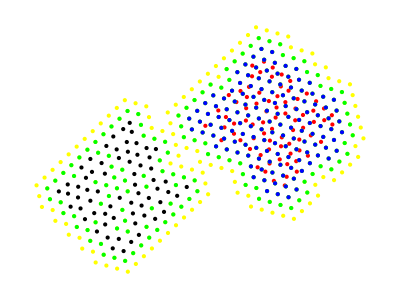
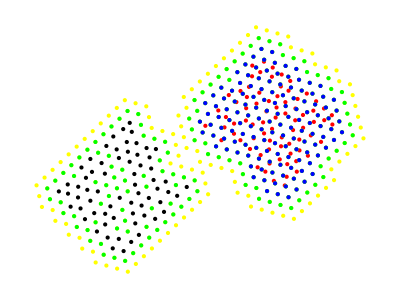
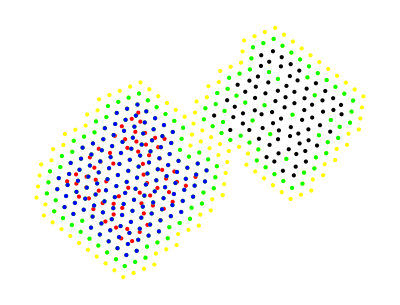
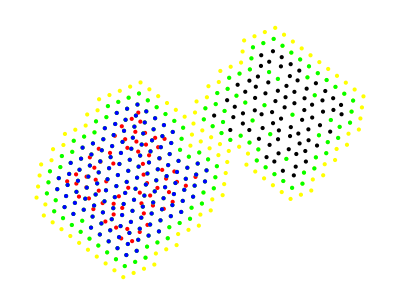
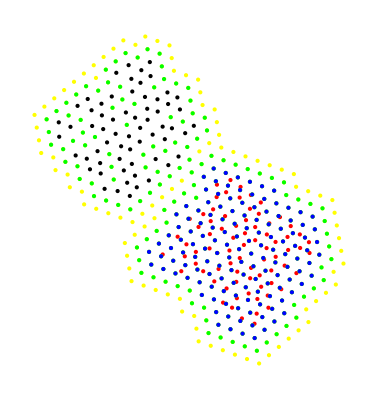
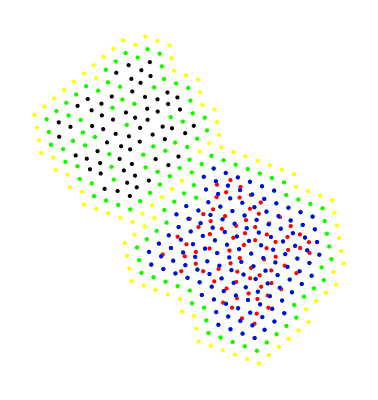
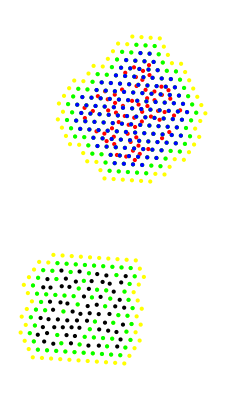
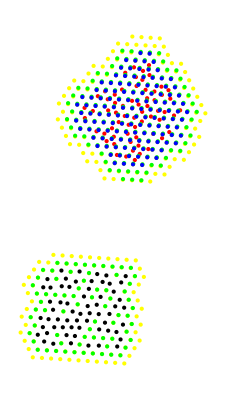

```mathematica
graphGrow[pts_,samples_,npts0_,npts1_, npts2_]:=Module[{},
Graphics[{Map[Point,pts],{Red,Map[Point,samples]},{Yellow,Map[Point,npts2]},{Green,Map[Point,npts1]},{Blue,Map[Point,npts0]}}]
];
importedData = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\growResults.json"];
importedPlots:=Map[(graphGrow[#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]])&,importedData];
mathematicaPlots:=Map[(graphGrow[
#[[1]],#[[2]],
growAndCover[#[[1]],#[[2]],0,75],
growAndCover[#[[1]],#[[2]],1,75],
growAndCover[#[[1]],#[[2]],2,75]
])&,importedData];
Column[Transpose[{importedPlots,mathematicaPlots}]]
```

## TSV Import Unit Tests

### Functions

```mathematica
getClusterArray[n_,i_]:=Module[{arr=Table[0,{n}]},arr⟦i⟧=1;arr];
numRANSAC=5;
widBuffer=2;
```

```mathematica
loadTSV[fname_,sliceNames_,sliceInd_,tissueInd_,rowcolInds_,clusterInd_,featureInds_,zDis_,srctgts_]:=Module[{slices,vals,clusters,tab,records,nclusters,nfeatures,nm,xyInds=Reverse[rowcolInds],names,nslices},
tab=Import[fname];
names=Append[tab⟦1,featureInds⟧,"No tissue"];
tab=Drop[tab,1];

nclusters = Max[Select[tab⟦;;,clusterInd⟧,NumberQ]]+1;
nfeatures=Length[featureInds];
records=Map[(nm=#;Select[tab,(#⟦sliceInd⟧==nm&&#⟦tissueInd⟧==1)&])&,sliceNames];
slices=Table[
If[i==1,
records⟦i,;;,xyInds⟧,
getTransSVD[srctgts⟦i-1,1⟧,srctgts⟦i-1,2⟧][records⟦i,;;,xyInds⟧]],
{i,Length[sliceNames]}];
clusters=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nclusters+1,nclusters+1],
getClusterArray[nclusters+1,#⟦clusterInd⟧+1]]&,#]&,records];
vals=Map[Map[If[#⟦tissueInd⟧==0,
getClusterArray[nfeatures+1,nfeatures+1],
Append[#⟦featureInds⟧,0]]&,#]&,records];

(* Add buffer to each slice and cover neighboring slices *)
nslices=Table[
Switch[i,
1,
growAndCover[slices⟦i⟧,slices⟦i+1⟧,widBuffer,numRANSAC],
Length[slices],
growAndCover[slices⟦i⟧,slices⟦i-1⟧,widBuffer,numRANSAC],
_,
growAndCover[slices⟦i⟧,Join[slices⟦i-1⟧,slices⟦i+1⟧],widBuffer,numRANSAC]],{i,Length[slices]}];

slices=Table[Map[Append[#,i*zDis]&,Join[slices⟦i⟧,nslices⟦i⟧]],{i,Length[slices]}];
clusters=MapThread[Join[#1,Map[getClusterArray[nclusters+1,nclusters+1]&,#2]]&,{clusters,nslices}];
vals=MapThread[Join[#1,Map[getClusterArray[nfeatures+1,nfeatures+1]&,#2]]&,{vals,nslices}];

(* add empty top and bottom slices *)
slices=Prepend[Append[slices,Map[(#+{0,0,zDis})&,Last[slices]]],Map[(#+{0,0,-zDis})&,First[slices]]];
clusters=
Prepend[Append[clusters,
Map[getClusterArray[nclusters+1,nclusters+1]&,Last[slices]]],
Map[getClusterArray[nclusters+1,nclusters+1]&,First[slices]]];
vals=
Prepend[Append[vals,
Map[getClusterArray[nfeatures+1,nfeatures+1]&,Last[slices]]],
Map[getClusterArray[nfeatures+1,nfeatures+1]&,First[slices]]];

{slices,clusters,vals,names}
]
```

## 2D Contour Tests

#### 2D Contour Implementation

```mathematica
orientation[u_,v_]:=Sign[Cross[Append[u,0],Append[v,0]]⟦3⟧];
```

```mathematica
getMaxPos[vals_]:=MaximalBy[Range[Length[vals]],vals⟦#⟧&]⟦1⟧;
```

```mathematica
getMassPoint[pts_]:=Mean[Select[pts,#≠{}&]];
```

```mathematica
interpEdge2Mat[p_,q_,pvals_,qvals_]:=Module[
{t=Abs[pvals⟦1⟧-pvals⟦2⟧]/(Abs[pvals⟦1⟧-pvals⟦2⟧]+Abs[qvals⟦1⟧-qvals⟦2⟧])},
(1-t)p+t*q
];
```

```mathematica
contourTriMultiDC[pts_,tris_,vals_]:=Module[{ptMats,nmat=Length[vals⟦1⟧],verts,segs,segMats,edgeHash,edges,edgeFaces,edgePtInds,npts=Length[pts],ntris=Length[tris],edgeMap={{1,2},{2,3},{3,1}},ind,edgePoints,triVertInds,newseg,ct,ct2,ct3,bdVertInd,fillVerts,fillTris,fillMats,seg},
(* get material index at each point *)
ptMats=Map[getMaxPos,vals];

(* create adj table from edges to faces *)
edgeHash[_,_]=0;
edges=Table[{},{ntris*3}];
edgeFaces=Table[{},{ntris*3}];
ct=0;
Do[If[(ind=edgeHash[
tris⟦i,edgeMap⟦j,1⟧⟧,
tris⟦i,edgeMap⟦j,2⟧⟧
])==0,
ct+=1;
edges⟦ct⟧=tris⟦i,edgeMap⟦j⟧⟧;
edgeFaces⟦ct⟧={i};
edgeHash[tris⟦i,edgeMap⟦j,1⟧⟧,tris⟦i,edgeMap⟦j,2⟧⟧]=ct;
edgeHash[tris⟦i,edgeMap⟦j,2⟧⟧,tris⟦i,edgeMap⟦j,1⟧⟧]=ct,
AppendTo[edgeFaces⟦ind⟧,i]],
{i,ntris},{j,3}];
edges=edges⟦1;;ct⟧;
edgeFaces=edgeFaces⟦1;;ct⟧;

(* create interpolation points, one per edge with material change *)
edgePoints=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧,
{},
interpEdge2Mat[pts⟦#⟦1⟧⟧,pts⟦#⟦2⟧⟧,vals⟦#⟦1⟧,ptMats⟦#⟧⟧,vals⟦#⟦2⟧,ptMats⟦#⟧⟧]]&,edges];
edgePtInds=Table[0,{Length[edges]}];

(* create vertices, one per triangle with material change *)
verts=Table[{},{ntris*7}];
ct=0;
triVertInds=Map[
If[ptMats⟦#⟦1⟧⟧==ptMats⟦#⟦2⟧⟧==ptMats⟦#⟦3⟧⟧,
0,
ind=#;
ct+=1;
verts⟦ct⟧=getMassPoint[edgePoints⟦Map[edgeHash[ind⟦#⟦1⟧⟧,ind⟦#⟦2⟧⟧]&,edgeMap]⟧];
ct]&,
tris];

(* create segments *)
segs=Table[{},{Length[edges]}];
segMats=Table[{},{Length[edges]}];
ct2=0;
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
ct2+=1;
segMats⟦ct2⟧=ptMats⟦edges⟦i⟧⟧;
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
ct+=1;
verts⟦ct⟧=edgePoints⟦i⟧;
edgePtInds⟦i⟧=ct;
newseg={triVertInds⟦edgeFaces⟦i,1⟧⟧,ct},
(* interior edge: connect two triangle points *)
newseg=triVertInds⟦edgeFaces⟦i⟧⟧];
If[orientation[pts⟦edges⟦i,1⟧⟧-pts⟦edges⟦i,2⟧⟧,verts⟦newseg⟦1⟧⟧-pts⟦edges⟦i,1⟧⟧]<0,
newseg=Reverse[newseg]];
segs⟦ct2⟧=newseg],
{i,Length[edges]}];

verts=verts⟦1;;ct⟧;
segs=segs⟦1;;ct2⟧;
segMats=segMats⟦1;;ct2⟧;

(* create fill triangles *)
fillVerts=Join[verts,pts];
fillTris=Table[{},{ntris*6}];
fillMats=Table[0,{ntris*6}];
ct3=0;

(* first type of triangles: dual to mesh edges with a material change *)
Do[
If[ptMats⟦edges⟦i,1⟧⟧≠ptMats⟦edges⟦i,2⟧⟧,
If[Length[edgeFaces⟦i⟧]==1,
(* boundary edge: connect edge point and triangle point *)
seg={triVertInds⟦edgeFaces⟦i,1⟧⟧,edgePtInds⟦i⟧},
(* interior edge: connect two triangle points *)
seg=triVertInds⟦edgeFaces⟦i⟧⟧];
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,1⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,1⟧⟧;
ct3+=1;
fillTris⟦ct3⟧=Append[seg,ct+edges⟦i,2⟧];
fillMats⟦ct3⟧=ptMats⟦edges⟦i,2⟧⟧],
{i,Length[edges]}];

(* second type of triangles: original mesh triangle, if there is no material change, or a third of the triangle, if there is some edge with no material change *)
Do[If[ptMats⟦tris⟦i,1⟧⟧==ptMats⟦tris⟦i,2⟧⟧==ptMats⟦tris⟦i,3⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=tris⟦i⟧+{ct,ct,ct};
fillMats⟦ct3⟧=ptMats⟦tris⟦i,1⟧⟧,
Do[If[ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧==ptMats⟦tris⟦i,edgeMap⟦j,2⟧⟧⟧,
ct3+=1;
fillTris⟦ct3⟧=Append[tris⟦i,edgeMap⟦j⟧⟧+{ct,ct},triVertInds⟦i⟧];
fillMats⟦ct3⟧=ptMats⟦tris⟦i,edgeMap⟦j,1⟧⟧⟧],
{j,3}]],
{i,Length[tris]}];

(* Print[ct3,fillVerts,fillTris,fillMats]; *)
fillTris=fillTris⟦1;;ct3⟧;
fillMats=fillMats⟦1;;ct3⟧;

{verts,segs,segMats,fillVerts,fillTris,fillMats}
];
```

```mathematica
perp[{x_,y_}]:={-y,x}
```

```mathematica
getContourByMat2D[verts_,segs_,segmats_,mat_,shrink_]:=Module[{inds1,inds2,nsegs,nvertInds,nverts,vertUsed,vertNewInds,vertnorms,nm},
(* select segments by mat *)
inds1=Select[Range[Length[segs]],segmats⟦#,1⟧==mat&];
inds2=Select[Range[Length[segs]],segmats⟦#,2⟧==mat&];
nsegs=Join[segs⟦inds1⟧,Map[Reverse,segs⟦inds2⟧]];
(* prune unused vertices *)
vertUsed=Map[False&,verts];
Scan[(vertUsed⟦#⟦1⟧⟧=True;vertUsed⟦#⟦2⟧⟧=True)&,nsegs];
nvertInds=Pick[Range[Length[verts]],vertUsed];
vertNewInds=Map[0&,verts];
Do[vertNewInds⟦nvertInds⟦i⟧⟧=i,{i,Length[nvertInds]}];
nverts=verts⟦nvertInds⟧;
nsegs=Map[vertNewInds⟦#⟧&,nsegs,{2}];
(* shrink *)
vertnorms=Map[{0,0}&,nverts];
Scan[(nm=perp[nverts⟦#⟦2⟧⟧-nverts⟦#⟦1⟧⟧];
vertnorms⟦#⟦1⟧⟧+=nm;
vertnorms⟦#⟦2⟧⟧+=nm)&,nsegs];
nverts+=shrink*Map[Normalize,vertnorms];
{nverts,nsegs}];
```

```mathematica
getContourAllMats2D[verts_,segs_,segmats_,nmat_,shrink_]:=Table[getContourByMat2D[verts,segs,segmats,i,shrink],{i,nmat}];
```

```mathematica
getSectionContours[pts_,vals_,shrink_]:=Module[{tris,npts,z=pts⟦1,3⟧,reg,verts,segs,segmats,fverts,ftris,fmats, nmat=Length[vals⟦1⟧],ctrs},
npts=Map[#⟦{1,2}⟧&,pts];
reg=DelaunayMesh[npts];
tris=Map[First,MeshCells[reg,2]];
{verts,segs,segmats,fverts,ftris,fmats}=contourTriMultiDC[npts,tris,vals];
ctrs=getContourAllMats2D[verts,segs,segmats,nmat,shrink];
{Map[{Map[Append[#,z]&,#⟦1⟧],#⟦2⟧}&,ctrs],
{Map[Append[#,z]&,fverts],ftris,fmats}}];
```

```mathematica
getSectionContoursAll[sections_,vals_,shrink_]:=Transpose[MapThread[getSectionContours[#1,#2,shrink]&,{sections,vals}]];
```

#### Tests

```mathematica
{slices, clusters,vals,featureNames} = Import["C:\\Users\\Aiden McIlraith\\Documents\\GitHub\\st-visualizer\\importTsvResults.json"];
```

```mathematica
result = getSectionContoursAll[slices, vals, 1.0];
result[[2,1,1]];
```

```mathematica
result = getSectionContours[slices[[1]],vals[[1]],1.0]
```

{{808,968,674},{968,808,1512},{674,968,851},{1359,808,1901},{808,674,1901},{674,851,713},{1384,674,713},{1512,808,11},{427,968,364},{968,1512,364},{11,808,1359},{742,851,427},{851,968,427},{376,1901,1384},{1901,674,1384},{1621,713,566},{713,851,566},{1231,1512,1343},{1512,11,1343},{566,851,742},{573,364,1231},{364,1512,1231},{1437,1359,1502},{1359,1901,1502},{1502,1901,376},{369,1384,472},{1384,713,472},{1249,11,1761},{11,1359,1761},{147,427,1006},{427,364,1006},{472,713,1621},{566,742,466},{1343,11,1249},{742,427,147},{1166,1006,573},{1006,364,573},{1231,1343,1187},{376,1384,369},{19,1761,1437},{1761,1359,1437},{1820,566,466},{742,147,1581},{691,1231,1187},{1343,1249,1087},{1716,1502,1454},{1502,376,1454},{376,369,1315},{1404,1621,1820},{1621,566,1820},{1067,472,1621},{1187,1343,1087},{466,742,1581},{147,1006,1888},{331,573,691},{573,1231,691},{1187,1087,193},{1454,376,1315},{1263,472,1067},{903,1437,1716},{1437,1502,1716},{1263,369,472},{294,1249,1891},{1249,1761,1891},{1891,1761,19},{1073,369,1263},{1143,147,1888},{1888,1006,1166},{1067,1621,1404},{1820,466,1945},{466,1581,592},{1087,1249,294},{1581,147,1143},{1888,1166,1206},{766,1166,331},{1166,573,331},{222,19,903},{19,1437,903},{1853,1315,1073},{1315,369,1073},{23,1820,1945},{1581,1143,1145},{941,691,1187},{941,1187,193},{1087,294,856},{1945,466,592},{205,691,941},{646,1716,249},{1716,1454,249},{1454,1315,113},{249,1454,113},{960,1404,23},{1404,1820,23},{1945,592,1607},{771,193,856},{193,1087,856},{1342,1891,462},{943,1263,1766},{1263,1067,1766},{1067,1404,1304},{943,1073,1263},{1342,294,1891},{1891,19,462},{331,691,205},{941,193,237},{394,592,1145},{592,1581,1145},{916,1888,1206},{916,1143,1888},{331,205,503},{113,1315,1853},{1919,903,646},{903,1716,646},{249,113,1662},{113,1853,629},{1766,1067,1304},{600,294,1342},{462,19,222},{194,1073,943},{1494,1143,916},{1193,1206,766},{1206,1166,766},{1511,1304,960},{1304,1404,960},{856,294,600},{1145,1143,1494},{581,1206,1193},{766,331,503},{1100,941,237},{662,222,1919},{222,903,1919},{1570,1853,194},{1853,1073,194},{1441,1766,1009},{588,23,1945},{588,1945,1607},{1145,1494,1516},{1100,205,941},{856,600,844},{962,646,249},{962,249,1662},{1872,23,588},{237,193,771},{811,1607,394},{1607,592,394},{1646,205,1100},{71,646,962},{1662,113,629},{1441,943,1766},{1766,1304,1009},{960,23,1872},{1342,462,521},{462,222,1626},{499,1342,521},{499,600,1342},{1596,943,1441},{521,462,1626},{581,916,1206},{766,503,796},{1821,1494,916},{1821,916,581},{493,960,1872},{1093,771,844},{771,856,844},{1349,503,1646},{503,205,1646},{1207,237,867},{829,394,1516},{394,1145,1516},{1348,1919,71},{1919,646,71},{962,1662,1461},{1662,629,110},{151,629,1570},{629,1853,1570},{194,943,1596},{1790,600,499},{521,1626,545},{910,1009,1511},{1009,1304,1511},{1553,194,1596},{1441,1009,1159},{1626,222,662},{1810,1193,796},{1193,766,796},{418,1494,1821},{1511,960,493},{984,588,1261},{844,600,1790},{1683,521,545},{984,1872,588},{588,1607,1261},{1207,1100,237},{237,771,867},{844,1790,126},{1261,1607,811},{1458,1100,1207},{543,1516,418},{1516,1494,418},{1550,796,1349},{796,503,1349},{1646,1100,1458},{1570,194,1553},{925,1441,1159},{373,662,1348},{662,1919,1348},{1227,71,962},{1227,962,1461},{1570,1553,1971},{1461,1662,110},{351,1872,984},{867,771,1093},{1308,811,829},{811,394,829},{1743,1646,1458},{1207,867,1430},{110,629,151},{1505,71,1227},{925,1596,1441},{1511,493,375},{1683,499,521},{1626,662,570},{1625,581,524},{581,1193,524},{1625,1821,581},{1159,1009,910},{493,1872,351},{1385,499,1683},{660,1553,1596},{660,1596,925},{1159,910,1958},{545,1626,570},{1348,71,1505},{524,1193,1810},{1349,1646,1743},{783,418,1821},{783,1821,1625},{524,1810,622},{976,493,351},{833,1093,126},{1093,844,126},{1790,499,1385},{1496,829,543},{829,1516,543},{1470,1349,1743},{199,151,1971},{151,1570,1971},{1789,1348,1505},{800,1461,1873},{1461,110,1873},{910,1511,375},{1046,1790,1385},{1683,545,157},{545,570,123},{570,662,373},{555,1553,660},{1837,418,783},{1371,1810,1550},{1810,796,1550},{831,1207,1430},{867,1093,1803},{831,1458,1207},{1290,1261,1248},{1261,811,1248},{1290,984,1261},{800,1227,1461},{110,151,881},{1438,351,984},{1438,984,1290},{1430,867,1803},{1248,811,1308},{1079,1458,831},{1430,1803,1400},{1873,110,881},{1906,1227,800},{1398,375,976},{375,493,976},{105,126,1046},{126,1790,1046},{159,543,1837},{543,418,1837},{872,1550,1470},{1550,1349,1470},{1743,1458,1079},{999,1971,555},{1971,1553,555},{1541,925,1159},{965,373,1789},{373,1348,1789},{1505,1227,1906},{1834,570,373},{445,351,1438},{1290,1248,1515},{1803,1093,833},{1541,777,925},{1541,1159,1958},{910,375,823},{1707,1385,1683},{1707,1683,157},{777,660,925},{1085,1743,1079},{1672,1430,1400},{157,545,123},{1565,1308,1496},{1308,829,1496},{1119,1625,511},{1625,524,511},{1119,783,1625},{511,524,622},{1028,1505,1906},{711,881,199},{881,151,199},{1173,1385,1707},{1294,1958,823},{1958,910,823},{1825,660,777},{123,570,1834},{622,1810,1371},{1125,1837,783},{1125,783,1119},{511,622,1340},{622,1371,453},{354,976,445},{976,351,445},{512,1290,1515},{833,126,105},{1046,1385,1173},{1496,543,159},{2068,1470,1085},{1470,1743,1085},{1672,831,1430},{1047,1789,1028},{1789,1505,1028},{1463,199,999},{199,1971,999},{555,660,1825},{823,375,1398},{1425,1046,1173},{1868,157,201},{1401,555,1825},{422,1541,1499},{1209,1834,965},{1834,373,965},{1371,1550,872},{1092,1837,1125},{512,1438,1290},{1248,1308,1026},{1496,159,1893},{1672,1381,831},{1803,833,224},{833,105,933},{1515,1248,1026},{1381,1079,831},{308,1873,1136},{1873,881,1136},{308,800,1873},{308,874,800},{874,1906,800},{1475,1438,512},{1400,1803,224},{105,1046,1425},{938,1026,1565},{1026,1308,1565},{159,1837,1092},{1885,1079,1381},{1672,1400,382},{1180,1136,711},{1136,881,711},{999,555,1401},{67,1028,1906},{67,1906,874},{1632,1398,354},{1398,976,354},{445,1438,1475},{1653,105,1425},{1868,1707,157},{872,1470,2068},{1085,1079,1885},{422,777,1541},{1541,1958,1499},{823,1398,1177},{1868,1619,1707},{157,123,201},{123,1834,913},{1681,159,1092},{1041,999,1401},{1664,777,422},{1832,965,1047},{965,1789,1047},{723,1119,511},{723,511,1340},{1371,872,2069},{872,2068,2036},{723,951,1119},{1499,1958,1294},{1619,1173,1707},{1664,1825,777},{1817,201,913},{201,123,913},{951,1125,1119},{1340,622,453},{424,445,1475},{1491,1515,108},{1460,224,933},{224,833,933},{233,1565,1893},{1565,1496,1893},{2085,1085,1885},{1309,1028,67},{795,711,1463},{711,199,1463},{1962,1294,1177},{1294,823,1177},{453,1371,2069},{2068,1085,2085},{1040,1425,1173},{1040,1173,1619},{1868,201,1273},{1710,1825,1664},{554,1499,731},{913,1834,1209},{1589,1125,951},{1163,1340,2001},{426,354,424},{354,445,424},{1491,512,1515},{933,105,1653},{2037,2068,2085},{1893,159,1681},{1092,1125,1589},{1463,999,1041},{1401,1825,1710},{48,1047,1309},{1047,1028,1309},{969,874,308},{1177,1398,1632},{149,1425,1040},{2035,2069,2036},{2069,872,2036},{1491,166,512},{1515,1026,108},{1893,1681,1444},{1366,1672,382},{1400,224,1734},{933,1653,1008},{1366,1381,1672},{1366,299,1381},{200,1401,1710},{554,422,1499},{429,1209,1832},{1209,965,1832},{1587,1092,1589},{1163,723,1340},{1340,453,2001},{969,308,1212},{308,1136,1212},{1463,1041,909},{969,47,874},{166,1475,512},{382,1400,1734},{108,1026,938},{299,1885,1381},{382,1734,1921},{47,67,874},{1212,1136,1180},{1169,1475,166},{1734,224,1460},{1653,1425,149},{754,938,233},{938,1565,233},{1681,1092,1587},{615,2085,1885},{615,1885,299},{1180,711,795},{1041,1401,200},{914,1309,67},{914,67,47},{969,1212,1764},{1212,1180,1453},{1180,795,56},{1163,403,723},{453,2069,2040},{554,1551,422},{1499,1294,731},{1177,1632,488},{1875,1619,1868},{1875,1868,1273},{913,1209,406},{1551,1664,422},{1273,201,1817},{403,951,723},{1795,1632,426},{1632,354,426},{424,1475,1169},{1154,1653,149},{1661,1619,1875},{731,1294,1962},{1996,2001,2040},{2001,453,2040},{2036,2068,2037},{2038,2036,2037},{1661,1040,1619},{1273,1817,1684},{607,1664,1551},{607,1710,1664},{174,1817,406},{1817,913,406},{1832,1047,48},{269,1681,1587},{803,951,403},{929,1041,200},{921,1832,48},{803,1589,951},{1014,424,1169},{337,1491,752},{1491,108,752},{644,1460,1008},{1460,933,1008},{1284,233,1444},{233,1893,1444},{54,2085,615},{98,1366,382},{795,1463,909},{502,1309,914},{1897,1962,488},{1962,1177,488},{426,424,1014},{265,1040,1661},{2041,2040,2035},{2040,2069,2035},{2037,2085,54},{1310,200,1710},{1310,1710,607},{1617,554,604},{554,731,604},{406,1209,429},{862,1589,803},{196,1163,1599},{337,166,1491},{108,938,612},{98,747,1366},{98,382,1921},{1734,1460,898},{752,108,612},{747,299,1366},{432,47,969},{432,969,1764},{795,909,1518},{1764,1212,1453},{1072,426,1014},{1325,166,337},{814,1008,1154},{1008,1653,1154},{149,1040,265},{1082,1444,269},{1444,1681,269},{1587,1589,862},{72,2037,54},{2065,299,747},{145,909,929},{909,1041,929},{397,48,502},{48,1309,502},{1894,47,432},{488,1632,1795},{1325,1169,166},{114,149,265},{1337,1921,898},{1921,1734,898},{2034,2035,2038},{2035,2036,2038},{612,938,754},{2065,615,299},{1030,200,1310},{1549,429,921},{429,1832,921},{1965,1587,862},{196,403,1163},{1894,914,47},{1764,1453,1417},{1453,1180,56},{1617,1551,554},{731,1962,1222},{488,1795,794},{1617,1019,1551},{1352,1875,1273},{1352,1273,1684},{406,429,1450},{1352,1103,1875},{196,995,403},{1163,2001,1599},{306,1014,1169},{306,1169,1325},{423,752,1001},{752,612,1001},{898,1460,644},{1599,2001,1996},{604,731,1222},{2064,615,2065},{963,98,1074},{1103,1661,1875},{1019,607,1551},{235,1684,174},{1684,1817,174},{610,754,1284},{754,233,1284},{269,1587,1965},{995,803,403},{56,795,1518},{637,502,914},{637,914,1894},{669,1764,1417},{1453,56,757},{1222,1962,1897},{203,1996,2041},{1996,2040,2041},{2038,2037,72},{226,265,1661},{226,1661,1103},{553,1310,607},{553,607,1019},{957,604,1898},{604,1222,1898},{87,174,1450},{174,406,1450},{921,48,397},{27,803,995},{1392,1795,1072},{1795,426,1072},{119,1154,114},{1154,149,114},{1311,2038,72},{54,615,2064},{632,269,1965},{862,803,27},{15,929,1030},{929,200,1030},{1428,921,397},{1410,1014,306},{1216,644,814},{644,1008,814},{2095,54,2064},{1452,1284,1082},{1284,1444,1082},{278,1518,145},{1518,909,145},{1432,502,637},{1777,1897,794},{1897,488,794},{1072,1014,1410},{1669,265,226},{1311,608,2034},{2041,2035,2034},{1788,1310,553},{1450,429,1549},{1650,1965,862},{1650,862,27},{192,196,324},{423,301,337},{423,337,752},{612,754,780},{963,1324,747},{963,747,98},{98,1921,1074},{898,644,1413},{669,471,432},{669,432,1764},{56,1518,1970},{301,1325,337},{1074,1921,1337},{1783,1001,780},{1001,612,780},{1324,2065,747},{471,1894,432},{1792,1417,757},{1417,1453,757},{1411,1072,1410},{243,1325,301},{243,306,1325},{423,1001,955},{1216,708,1413},{1337,898,1413},{814,1154,119},{305,814,119},{114,265,1669},{72,54,2095},{2066,2065,1324},{2048,72,2095},{780,754,610},{2066,2064,2065},{769,1074,1337},{541,1082,632},{1082,269,632},{1152,397,1432},{397,502,1432},{1667,1894,471},{1208,145,15},{145,929,15},{1030,1310,1788},{757,56,1970},{1667,637,1894},{164,1417,1792},{794,1795,1392},{458,114,1669},{1431,1103,1352},{1431,1352,118},{1352,1684,118},{319,1030,1788},{957,137,1617},{957,1617,604},{1195,1549,1428},{1549,921,1428},{1297,2041,2034},{2034,2038,1311},{1718,1965,1650},{192,995,196},{196,1599,324},{1617,137,1019},{1222,1897,1292},{794,1392,1286},{1431,169,1103},{1450,1549,21},{137,153,1019},{118,1684,235},{192,563,995},{1599,1996,411},{324,1599,411},{1898,1222,1292},{169,226,1103},{153,553,1019},{1794,235,87},{235,174,87},{1744,411,203},{411,1996,203},{563,27,995},{324,411,1282},{1801,1410,306},{1801,306,243},{1413,644,1216},{2063,2064,2066},{2063,2095,2064},{582,610,1452},{610,1284,1452},{632,1965,1718},{707,1970,278},{1970,1518,278},{15,1030,319},{379,637,1667},{164,669,1417},{379,1432,637},{1064,1292,1777},{1292,1897,1777},{1895,226,169},{1305,553,153},{92,957,671},{87,1450,21},{1953,27,563},{1746,203,1297},{203,2041,1297},{357,1392,1411},{1392,1072,1411},{1851,119,458},{119,114,458},{1669,226,1895},{1375,1311,2048},{1311,72,2048},{1414,632,1718},{1650,27,1953},{979,15,319},{1788,553,1305},{385,1428,1152},{1428,397,1152},{414,1410,1801},{1016,1216,305},{1216,814,305},{487,1337,1413},{769,1890,1074},{1930,2095,2063},{1452,1082,541},{94,278,1208},{278,145,1208},{1658,1432,379},{52,1777,1286},{1777,794,1286},{1876,1669,1895},{966,1431,118},{966,118,1732},{361,301,423},{361,423,955},{780,610,1162},{1452,541,848},{361,1096,301},{1890,539,963},{1890,963,1074},{963,539,1324},{955,1001,1783},{539,2060,1324},{1176,1788,1305},{92,137,957},{1723,21,1195},{21,1549,1195},{229,1650,1953},{906,192,324},{1297,2034,608},{2048,2095,1930},{669,1104,471},{164,1104,669},{757,1970,1806},{1104,221,471},{1096,243,301},{955,1783,57},{769,1337,487},{1783,780,1162},{2060,2066,1324},{1409,769,487},{1506,1792,1806},{1792,757,1806},{221,1667,471},{160,243,1096},{160,1801,243},{1016,967,708},{487,1413,708},{957,1898,671},{1898,1292,1339},{92,1132,137},{2062,2063,2066},{2062,2066,2060},{966,602,1431},{118,235,1732},{87,21,275},{848,1301,582},{1002,1162,582},{1162,610,582},{541,632,1414},{1767,1411,414},{1411,1410,414},{906,1281,192},{906,324,1282},{1297,608,904},{1259,305,1851},{305,119,1851},{458,1669,1876},{986,379,1667},{986,1667,221},{109,164,381},{1289,1806,707},{1806,1970,707},{671,1898,1339},{602,169,1431},{1132,153,137},{317,1339,1064},{1918,1732,1794},{1732,235,1794},{371,541,1414},{1718,1650,229},{1285,2048,1930},{1208,15,979},{319,1788,1176},{290,1208,979},{828,1152,1658},{1152,1432,1658},{385,1195,1428},{1923,1286,357},{1286,1392,357},{1281,563,192},{1282,411,1744},{608,1311,1375},{1904,458,1876},{93,169,602},{1317,319,1176},{556,153,1132},{1578,1195,385},{120,608,1375},{1313,1718,229},{1588,563,1281},{1339,1292,1064},{93,1895,169},{556,1305,153},{1706,1794,275},{1794,87,275},{1588,1953,563},{906,1282,1210},{1282,1744,1601},{1798,1744,1746},{1744,203,1746},{1937,1801,160},{1561,487,708},{708,1216,1016},{1851,458,1904},{930,1890,769},{930,1341,1890},{1870,2063,2062},{1241,1783,1162},{582,1452,848},{1414,1718,1313},{1765,707,94},{707,278,94},{979,319,1317},{758,1658,379},{758,379,986},{109,1104,164},{164,1792,381},{1923,1406,52},{1064,1777,52},{357,1411,1767},{1328,1876,1895},{1328,1895,93},{1905,966,1118},{966,1732,1118},{1618,1176,1305},{1618,1305,556},{1171,1191,671},{275,21,1723},{1746,1297,904},{810,1953,1588},{1484,357,1767},{414,1801,1937},{1069,1851,1904},{26,1414,1313},{229,1953,810},{1696,1375,1285},{1375,2048,1285},{1930,2063,1870},{1280,979,1317},{154,385,828},{385,1152,828},{568,361,955},{568,955,57},{568,1387,361},{1341,882,539},{1341,539,1890},{405,414,1937},{1387,1096,361},{936,1016,1259},{1016,305,1259},{1387,1670,1096},{930,769,1409},{109,396,1104},{189,57,1241},{57,1783,1241},{882,2061,2060},{882,2060,539},{549,848,371},{848,541,371},{685,1930,1870},{678,94,290},{94,1208,290},{523,1658,758},{396,221,1104},{381,1792,1506},{396,870,221},{381,1506,1845},{1137,1064,52},{52,1286,1923},{1171,671,1339},{671,1191,92},{937,1876,1328},{937,1904,1876},{952,1176,1618},{1191,1951,92},{698,1723,1578},{1723,1195,1578},{828,1658,523},{821,229,810},{1156,1281,906},{135,904,120},{904,608,120},{1670,160,1096},{568,57,1120},{967,1701,1561},{1409,487,1561},{1241,1162,1002},{2061,2062,2060},{870,986,221},{1497,1506,1289},{1506,1806,1289},{92,1951,1132},{1905,1721,602},{1905,602,966},{275,1723,508},{1951,1711,1132},{1118,1732,1918},{1156,516,1281},{1156,906,1210},{1746,904,1266},{1210,1282,1601},{1449,160,1670},{762,1409,1561},{1561,708,967},{1892,930,1409},{1952,1171,317},{1171,1339,317},{1721,93,602},{1185,2062,2061},{712,1341,930},{712,930,1892},{1711,556,1132},{551,1918,1706},{1918,1794,1706},{1141,1002,1301},{1002,582,1301},{371,1414,26},{1601,1744,1798},{516,1588,1281},{1210,1601,230},{577,986,870},{627,1289,1765},{1289,707,1765},{290,979,1280},{1317,1176,952},{1130,1767,405},{1767,414,405},{1937,160,1449},{1546,1259,1069},{1259,1851,1069},{1623,371,26},{1313,229,821},{1285,1930,685},{1870,2062,1185},{680,1285,685},{1696,120,1375},{51,1923,1484},{1923,357,1484},{500,1904,937},{443,93,1721},{167,290,1280},{843,828,523},{758,986,577},{1296,1317,952},{1824,556,1711},{1568,1313,821},{1647,1588,516},{529,1578,154},{1578,385,154},{1627,120,1696},{317,1064,1137},{443,1328,93},{1886,1118,298},{1824,1618,556},{562,1191,6},{1192,1706,508},{1706,275,508},{1861,1798,1266},{1798,1746,1266},{1647,810,1588},{1677,1210,230},{892,1937,1449},{1181,1387,568},{967,1016,936},{1694,1870,1185},{712,1291,1341},{1301,848,549},{408,821,810},{1251,1301,549},{1852,1241,1002},{1765,94,678},{1280,1317,1296},{366,758,577},{818,1137,1406},{1137,52,1406},{1484,1767,1130},{1830,937,1328},{1830,1328,443},{1886,1905,1118},{1066,1618,1824},{508,1723,698},{408,810,1647},{1568,26,1313},{1250,1266,135},{1266,904,135},{1696,1285,680},{1627,1012,135},{1181,1640,1387},{1181,568,1120},{1341,1291,882},{967,936,359},{1120,57,189},{1291,1751,882},{987,109,1383},{109,381,1383},{1765,678,1504},{987,396,109},{987,718,396},{1383,381,1845},{1214,1484,1130},{405,1937,892},{131,1069,500},{1069,1904,500},{1640,1099,1670},{1640,1670,1387},{1120,189,719},{1892,1409,762},{739,189,1852},{189,1241,1852},{1751,2061,882},{241,1892,762},{448,1696,680},{685,1870,1694},{1929,26,1568},{154,828,843},{523,758,366},{198,154,843},{336,1280,1296},{952,1618,1066},{1274,1845,1497},{1845,1506,1497},{678,290,167},{718,1700,870},{718,870,396},{1383,1845,896},{1940,405,892},{1287,936,1546},{936,1259,1546},{1758,549,1623},{549,371,1623},{1235,685,1694},{1237,2061,1751},{498,678,167},{1427,523,366},{1406,1923,51},{1130,405,1940},{1099,1449,1670},{234,937,1830},{1071,762,1701},{762,1561,1701},{1531,712,1892},{1852,1002,1141},{1237,1185,2061},{681,712,1531},{1479,952,1066},{562,1902,1951},{599,698,529},{698,1578,529},{843,523,1427},{1510,821,408},{1677,1780,1156},{879,1601,1798},{135,120,1627},{680,685,1235},{1951,1902,1711},{562,1951,1191},{1191,1171,6},{317,1137,1797},{1406,51,1363},{1497,1289,627},{1886,923,1905},{1118,1918,298},{508,698,1498},{1905,923,1721},{1700,577,870},{6,1171,1952},{923,693,1721},{1156,1780,516},{1677,1156,1210},{1902,699,1711},{298,1918,551},{230,1601,879},{1780,1459,516},{142,1952,1797},{1952,317,1797},{693,443,1721},{699,1824,1711},{1597,551,1192},{551,1706,1192},{1763,1449,1099},{1701,967,359},{1459,1647,516},{721,879,1861},{879,1798,1861},{1044,1141,1251},{1141,1301,1251},{1623,26,1929},{1345,1185,1237},{681,1291,712},{1345,1694,1185},{1866,627,1504},{627,1765,1504},{167,1280,336},{1296,952,1479},{66,577,1700},{1390,987,1383},{1214,51,1484},{1686,1130,1940},{892,1449,1763},{447,1546,131},{1546,1069,131},{500,937,234},{1323,51,1214},{1620,1623,1929},{1568,821,1510},{1972,680,1235},{456,500,234},{338,443,693},{1797,1137,818},{338,1830,443},{1448,1886,1194},{1886,298,1194},{1579,167,336},{198,529,154},{231,843,1427},{366,577,66},{939,1066,1824},{939,1824,699},{60,562,6},{1326,1192,1498},{1192,508,1498},{728,1296,1479},{1298,1568,1510},{1077,1647,1459},{73,529,198},{1045,1627,448},{1627,1696,448},{1077,408,1647},{1691,1677,230},{1691,230,510},{703,1861,1250},{1861,1266,1250},{1293,892,1763},{1042,206,1181},{1042,1181,1120},{1293,1940,892},{1762,359,1287},{359,936,1287},{390,1251,1758},{1251,549,1758},{155,1510,408},{481,1852,1141},{1737,1694,1345},{681,1786,1291},{1039,1427,366},{1039,366,66},{1390,1571,987},{211,1504,498},{1504,678,498},{336,1296,728},{1562,1497,627},{1181,206,1640},{1042,1120,719},{1291,1786,1751},{1701,359,1785},{538,818,1363},{818,1406,1363},{1883,234,1830},{1883,1830,338},{206,264,1640},{1531,1892,241},{1144,719,739},{719,189,739},{1786,1659,1751},{341,241,1071},{987,1571,718},{1390,1383,896},{1525,1066,939},{60,584,562},{1498,698,599},{1298,1929,1568},{155,408,1077},{1691,1369,1677},{746,1250,1012},{1250,135,1012},{448,680,1972},{1235,1694,1737},{510,230,879},{1571,1603,718},{1648,896,1274},{896,1845,1274},{264,1099,1640},{241,762,1071},{1105,739,481},{739,1852,481},{1659,1237,1751},{1274,1497,1562},{1603,1700,718},{1390,896,304},{413,1214,1686},{1214,1130,1686},{80,131,456},{131,500,456},{1961,448,1972},{477,1929,1298},{767,336,728},{1479,1066,1525},{1048,198,231},{198,843,231},{271,1700,1603},{1110,1940,1293},{148,1099,264},{1003,1287,447},{1287,1546,447},{60,6,614},{6,1952,614},{1797,818,1487},{562,584,1902},{1448,923,1886},{298,551,141},{1498,599,1729},{1448,1389,923},{584,1770,1902},{1194,298,141},{1265,1758,1620},{1758,1623,1620},{148,1763,1099},{1645,1235,1737},{1429,1237,1659},{1396,1071,1785},{1071,1701,1785},{927,1531,241},{927,696,1531},{498,167,1579},{62,498,1579},{949,1427,1039},{1677,1369,1780},{481,1141,1044},{1369,895,1780},{1429,1345,1237},{696,681,1531},{689,1363,1323},{1363,51,1323},{44,234,1883},{1389,693,923},{614,1952,142},{1389,809,693},{1194,141,1050},{1770,1529,699},{1770,699,1902},{91,614,142},{1909,1562,1866},{1562,627,1866},{141,551,1597},{599,529,73},{271,66,1700},{171,1390,304},{793,728,1479},{793,1479,1525},{1168,599,73},{231,1427,949},{983,1510,155},{895,1459,1780},{2107,1012,1045},{1012,1627,1045},{172,510,721},{510,879,721},{895,2059,1459},{288,142,1487},{142,1797,1487},{528,60,614},{809,338,693},{1804,1194,1050},{1529,939,699},{507,60,528},{1939,1597,1326},{1597,1192,1326},{2059,1077,1459},{2181,721,703},{721,1861,703},{817,1293,1763},{817,1763,148},{1175,206,1042},{1175,1042,1299},{1785,359,1762},{447,131,80},{1854,1044,390},{1044,1251,390},{1620,1929,477},{1225,1345,1429},{696,352,681},{1967,66,271},{961,1866,211},{1866,1504,211},{749,1686,1110},{1686,1940,1110},{413,1323,1214},{1841,447,80},{456,234,44},{613,338,809},{1487,818,538},{613,1883,338},{1540,1077,2059},{1593,1525,939},{1593,939,1529},{507,584,60},{676,1323,413},{1957,1326,1729},{1326,1498,1729},{595,231,949},{1739,456,44},{1021,1620,477},{1298,1510,983},{155,1077,1540},{1972,1235,1645},{1737,1345,1225},{227,1972,1645},{1961,1045,448},{977,1579,767},{1579,336,767},{1048,73,198},{1039,66,1967},{703,1250,746},{311,728,793},{363,1298,983},{1376,73,1048},{2148,1045,1961},{1175,1275,206},{1042,719,1299},{481,1044,609},{681,352,1786},{1785,1762,974},{1299,719,1144},{352,1839,1786},{639,1110,1293},{639,1293,817},{1275,264,206},{272,1762,1003},{1762,1287,1003},{80,456,1739},{171,437,1571},{171,1571,1390},{1274,1562,994},{304,896,1648},{262,390,1265},{390,1758,1265},{922,983,155},{1533,1645,1737},{1533,1737,1225},{1839,1659,1786},{1275,1736,264},{1396,1361,341},{927,241,341},{1513,1144,1105},{1144,739,1105},{1839,1547,1659},{451,949,1039},{451,1039,1967},{437,1603,1571},{578,211,62},{211,498,62},{767,728,311},{1648,1274,994},{437,1434,1603},{304,1648,1063},{920,538,689},{538,1363,689},{386,1883,613},{746,1012,2107},{1528,1525,1593},{507,849,584},{1528,793,1525},{1729,599,1168},{363,477,1298},{922,155,1540},{2106,1078,1369},{2106,1369,1691},{2106,1691,2139},{1736,148,264},{1000,927,341},{341,1071,1396},{232,696,927},{847,1105,609},{1105,481,609},{1547,1429,1659},{1218,696,232},{1434,271,1603},{518,994,1909},{994,1562,1909},{1369,1078,895},{1691,510,2139},{703,746,2247},{746,2107,2253},{584,849,1770},{1487,538,855},{1804,868,1448},{1804,1448,1194},{141,1597,1377},{1729,1168,88},{1448,868,1389},{528,614,91},{1078,2057,895},{868,50,1389},{849,684,1770},{1050,141,1377},{89,413,749},{413,1686,749},{1946,148,1736},{1841,1003,447},{17,80,1739},{44,1883,386},{2183,2139,172},{2139,510,172},{1021,1265,1620},{1651,477,363},{2147,1961,227},{1961,1972,227},{1507,767,311},{774,1048,595},{1048,231,595},{1503,1110,639},{1946,817,148},{161,1175,1299},{161,1299,1088},{1240,1003,1841},{1396,1785,974},{91,142,288},{50,1052,809},{50,809,1389},{1804,1050,1379},{172,721,2181},{2107,1045,2148},{684,1529,1770},{1419,528,532},{528,91,532},{942,1377,1939},{1377,1597,1939},{609,1044,1854},{1316,1225,1429},{1316,1429,1547},{945,1265,1021},{1321,1645,1533},{62,1579,977},{1644,62,977},{889,949,451},{1884,271,1434},{2057,2059,895},{2106,2139,2376},{1198,1909,961},{1909,1866,961},{1884,1967,271},{1812,171,304},{1812,304,1063},{1943,689,676},{689,1323,676},{738,1739,44},{738,44,386},{2377,2107,2148},{1910,793,1528},{1380,1529,684},{389,1168,1376},{1168,73,1376},{595,949,889},{575,983,922},{2058,2059,2057},{1738,288,855},{288,1487,855},{1052,613,809},{2058,1540,2059},{2438,2181,2247},{2181,703,2247},{1380,1593,1529},{332,1939,1957},{1939,1326,1957},{601,1050,1377},{1408,817,1946},{1408,639,817},{974,1762,272},{635,1854,262},{1854,390,262},{1021,477,1651},{1246,1225,1316},{1218,638,352},{961,211,578},{977,767,1507},{197,1967,1884},{855,538,920},{1327,749,1503},{158,613,1052},{574,868,1804},{1772,1540,2058},{2287,1078,2106},{2500,2247,2253},{2247,746,2253},{2118,227,1321},{89,676,413},{749,1110,1503},{737,1841,17},{1841,80,17},{386,613,158},{1957,1729,88},{1605,1593,1380},{1419,1114,507},{1419,507,528},{1605,1528,1593},{161,1031,1175},{1299,1144,1088},{609,1854,1270},{1175,1031,1275},{352,638,1839},{1218,352,696},{1396,974,958},{974,272,506},{30,676,89},{1805,1739,738},{1031,1813,1275},{232,927,1000},{227,1645,1321},{1533,1225,1246},{2147,2148,1961},{77,1021,1651},{363,983,575},{922,1540,1772},{2411,2148,2147},{1123,1088,1513},{1088,1144,1513},{638,355,1839},{1032,977,1507},{311,793,1910},{774,1376,1048},{799,595,889},{451,1967,197},{1812,885,171},{1648,994,291},{961,578,1086},{171,885,437},{1124,1376,774},{1552,311,1910},{238,363,575},{1063,1648,291},{885,1480,437},{1813,1567,1736},{1813,1736,1275},{173,232,1000},{751,1000,1361},{1000,341,1361},{272,1003,1240},{873,1513,847},{1513,1105,847},{355,1547,1839},{1243,232,173},{393,639,1408},{1150,272,1240},{17,1739,1805},{536,262,945},{262,1265,945},{1615,291,518},{291,994,518},{578,62,1644},{1480,421,1434},{1480,1434,437},{1812,1063,623},{1591,1533,1246},{812,1547,355},{14,578,1644},{1507,311,1552},{377,451,197},{410,920,1943},{920,689,1943},{89,749,1327},{1728,386,158},{574,34,868},{1728,738,386},{2506,2253,2377},{2253,2107,2377},{2147,227,2118},{1567,1946,1736},{853,161,850},{161,1088,850},{1361,1396,958},{1257,1528,1605},{88,1168,389},{774,595,799},{1262,88,389},{2287,2288,1078},{2287,2106,2376},{172,2181,2182},{2376,2139,2183},{507,1114,849},{91,288,621},{855,920,1935},{849,1114,168},{868,34,50},{574,1804,1379},{1957,88,415},{849,168,684},{1379,1050,601},{847,609,1270},{1378,575,922},{1378,922,1772},{2288,2057,1078},{812,1316,1547},{1243,1218,232},{421,1884,1434},{877,518,1198},{518,1909,1198},{532,91,621},{34,1188,50},{2288,2350,2057},{2376,2183,2441},{2440,2183,2182},{2183,172,2182},{168,1424,684},{1419,532,1465},{532,621,1197},{601,1377,942},{1964,89,1327},{1503,639,393},{729,1946,1567},{737,1240,1841},{928,17,1805},{621,288,1738},{1943,676,30},{1188,1052,50},{876,1379,591},{1379,601,591},{2350,2058,2057},{2439,2182,2438},{2182,2181,2438},{2411,2377,2148},{2387,2147,2118},{1321,1533,1591},{1424,1380,684},{1966,942,332},{942,1939,332},{729,1408,1946},{1215,958,506},{958,974,506},{1942,1651,238},{1651,363,238},{77,945,1021},{1827,774,799},{889,451,377},{561,1884,421},{1032,1644,977},{285,1507,1552},{1910,1528,1257},{1933,1503,393},{972,1270,635},{1270,1854,635},{792,1316,812},{1243,1914,1218},{792,1246,1316},{18,1240,737},{1198,961,1086},{561,197,1884},{1346,885,1812},{1346,1812,623},{1858,945,77},{2073,1321,1591},{1559,889,377},{700,1644,1032},{1598,1943,30},{1327,1503,1933},{309,1805,738},{309,738,1728},{1675,1052,1188},{2617,2377,2411},{2118,1321,2073},{1916,1552,1910},{1916,1910,1257},{1973,1380,1424},{1493,389,1124},{389,1376,1124},{1862,377,197},{1773,575,1378},{2142,2058,2350},{1773,238,575},{694,1738,1935},{1738,855,1935},{1675,158,1052},{2142,1772,2058},{2539,2287,2376},{2439,2438,2500},{2441,2539,2376},{2438,2247,2500},{1973,1605,1380},{1170,332,415},{332,1957,415},{1426,1408,729},{506,272,1150},{1776,635,536},{635,262,536},{77,1651,1942},{636,847,1270},{1768,1246,792},{1218,1914,638},{830,1086,14},{1086,578,14},{1559,799,889},{1862,197,561},{853,1778,1031},{853,1031,161},{1031,1778,1813},{638,1914,515},{1361,958,1879},{506,1150,43},{850,1088,1123},{638,515,355},{1935,920,410},{1566,1728,158},{1566,158,1675},{876,590,574},{876,574,1379},{601,942,540},{1778,641,1813},{885,1007,1480},{1346,1007,885},{1063,291,387},{1198,1086,736},{623,1063,387},{576,173,751},{173,1000,751},{626,1772,2142},{2500,2253,2506},{2140,2118,2073},{2439,2500,2506},{710,1123,873},{1123,1513,873},{515,1451,355},{1243,173,59},{788,1605,1973},{1911,1704,1114},{415,88,1262},{1964,30,89},{587,1327,1933},{393,1408,1426},{778,737,928},{737,17,928},{387,291,1615},{1007,1065,1480},{623,387,378},{387,1615,1634},{2387,2411,2147},{1591,1246,1768},{368,30,1964},{1481,1805,309},{1678,77,1942},{1378,1772,626},{2627,2411,2387},{894,1032,285},{1032,1507,285},{1257,1605,788},{1827,1124,774},{1295,799,1559},{641,1524,1567},{641,1567,1813},{751,1361,1879},{725,1552,1916},{1245,1124,1827},{74,238,1773},{785,873,636},{873,847,636},{536,945,1858},{1451,812,355},{323,1243,59},{1065,421,1480},{748,1615,877},{1615,518,877},{14,1644,700},{1871,393,1426},{204,1150,18},{1150,1240,18},{2287,2540,2288},{2539,2540,2287},{1911,1419,1465},{621,1738,1320},{1935,410,1080},{1911,1114,1419},{1114,1704,168},{574,590,34},{415,1262,1184},{1630,536,1858},{2074,2073,1591},{2074,1591,1768},{990,812,1451},{1465,532,1197},{2540,2541,2288},{590,279,34},{2441,2183,2440},{1704,652,168},{253,1197,1320},{1098,591,540},{591,601,540},{1950,377,1862},{1535,421,1065},{1642,14,700},{1608,410,1598},{410,1943,1598},{1964,1327,587},{1933,393,1871},{1524,729,1567},{1949,853,850},{1949,850,1514},{1403,1728,1566},{279,1188,34},{1403,309,1728},{1879,958,1215},{2645,2506,2617},{2506,2377,2617},{2387,2118,2140},{636,1270,972},{990,792,812},{323,1914,1243},{1247,1465,1197},{1197,621,1320},{208,1257,788},{652,1424,168},{208,1916,1257},{279,730,1188},{876,591,49},{1262,389,1493},{1827,799,1295},{840,1262,1493},{2541,2406,2350},{2541,2350,2288},{2440,2182,2439},{652,858,1424},{485,1465,1247},{540,942,1966},{779,1773,1378},{779,1378,626},{877,1198,736},{1535,561,421},{1320,1738,694},{730,1675,1188},{2406,2142,2350},{2540,2539,2531},{2539,2441,2531},{858,1973,1424},{485,1911,1465},{346,1966,1170},{1966,332,1170},{368,1598,30},{1714,1964,587},{195,1426,729},{195,729,1524},{1717,928,1481},{928,1805,1481},{1931,1215,43},{1215,506,43},{18,737,778},{2404,2387,2140},{656,972,1776},{972,635,1776},{254,1942,74},{1991,792,990},{323,1333,1914},{1991,1768,792},{1678,1858,77},{1942,238,74},{84,285,725},{285,1552,725},{932,1933,1871},{948,1827,1295},{1559,377,1950},{537,18,778},{329,736,830},{736,1086,830},{700,1032,894},{886,561,1535},{846,277,1346},{846,1346,623},{846,623,378},{886,1862,561},{2072,2073,2074},{717,1858,1678},{104,1598,368},{587,1933,932},{176,309,1403},{252,1675,730},{1814,1559,1950},{815,700,894},{2645,2617,2627},{2617,2411,2627},{2140,2073,2072},{694,1935,1080},{252,1566,1675},{1486,590,876},{2243,626,2142},{2243,2142,2406},{1874,725,1916},{1874,1916,208},{216,1973,858},{217,1493,1245},{1493,1124,1245},{1353,1950,1862},{695,74,1773},{695,1773,779},{216,788,1973},{485,544,1911},{1585,1170,1184},{1170,415,1184},{1949,1436,853},{850,1123,1514},{636,972,501},{853,1436,1778},{1914,1333,515},{751,1879,1760},{1879,1215,1594},{1436,682,1778},{59,173,576},{1514,1123,710},{1333,1536,515},{59,576,1182},{790,1426,195},{682,641,1778},{790,1871,1426},{1735,43,204},{43,1150,204},{778,928,1717},{1346,277,1007},{877,736,281},{2070,1768,1991},{1536,1451,515},{2070,2074,1768},{1776,536,1630},{1678,1942,254},{489,1776,1630},{277,1808,1007},{378,387,1634},{682,832,641},{1204,830,1642},{830,14,1642},{1814,1295,1559},{1353,1862,886},{1808,1065,1007},{576,751,1760},{733,710,785},{710,873,785},{1536,1351,1451},{1730,59,1182},{1080,410,1608},{786,1566,252},{1486,356,590},{1486,876,49},{786,1403,1566},{2244,626,2243},{2406,2541,2647},{2541,2540,2647},{2441,2440,2531},{1634,1615,748},{1808,266,1065},{846,378,1322},{378,1634,365},{1634,748,841},{864,788,216},{1911,544,1704},{864,208,788},{1184,1262,840},{1714,368,1964},{1416,587,932},{1741,778,1717},{1481,309,176},{832,1524,641},{128,1949,1840},{1949,1514,1840},{1760,1879,1594},{204,18,537},{2354,2140,2072},{533,368,1714},{1382,785,501},{785,636,501},{1351,990,1451},{1730,323,59},{1351,1990,990},{1679,1481,176},{1704,544,1682},{1320,694,1925},{694,1080,1347},{1080,1608,178},{590,356,279},{540,1966,1676},{1184,840,353},{2645,2627,2404},{2627,2387,2404},{1704,1682,652},{717,1630,1858},{761,1678,254},{779,626,2244},{49,591,1098},{1466,894,84},{894,285,84},{948,1245,1827},{45,1295,1814},{748,877,281},{266,1535,1065},{1668,725,1874},{236,1245,948},{1081,74,695},{1925,486,253},{1247,1197,253},{356,130,279},{49,1098,1896},{1682,1880,652},{1113,1098,1676},{1098,540,1676},{1108,932,1871},{1108,1871,790},{468,1524,832},{1202,204,537},{2071,2072,2074},{2071,2074,2070},{1816,1630,717},{468,195,1524},{630,1594,1931},{1594,1215,1931},{253,1320,1925},{988,1950,1353},{1395,1535,266},{130,730,279},{39,1642,815},{1642,700,815},{84,725,1668},{1509,1608,104},{1608,1598,104},{1880,858,652},{1172,485,1247},{1676,1966,346},{501,972,656},{1932,1403,786},{1083,730,130},{1990,1991,990},{715,779,2244},{649,281,329},{281,736,329},{1395,886,1535},{1563,1874,208},{1563,208,864},{65,858,1880},{840,1493,217},{948,1295,45},{1928,840,217},{178,347,1347},{1925,694,1347},{1083,252,730},{1539,1486,49},{2497,2243,2406},{2497,2406,2647},{2440,2439,2522},{2595,2404,2354},{65,216,858},{402,346,1585},{346,1170,1585},{1955,195,468},{128,579,1436},{1931,43,1735},{1011,1717,1679},{1717,1481,1679},{2050,1991,1990},{323,1867,1333},{956,1714,1416},{1714,587,1416},{790,195,1955},{1741,537,778},{176,1403,1932},{484,656,489},{656,1776,489},{446,254,1081},{2645,2439,2506},{2404,2140,2354},{2070,1991,2050},{1277,886,1395},{329,830,1204},{1302,329,1204},{1043,932,1108},{254,74,1081},{695,779,715},{2498,2243,2497},{761,717,1678},{340,537,1741},{1466,815,894},{190,84,1668},{1405,948,45},{1814,1950,988},{1353,886,1277},{2353,2072,2071},{31,717,761},{245,104,533},{104,368,533},{907,176,1932},{312,252,1083},{1509,1968,178},{1347,1080,178},{1347,441,1925},{253,1485,1247},{312,786,252},{1539,1846,1486},{1539,49,1896},{1775,815,1466},{871,1814,988},{128,1436,1949},{1514,710,1652},{501,656,606},{1436,579,682},{1730,1867,323},{576,1760,1556},{1760,1594,321},{1931,1735,763},{1333,1867,102},{2498,2244,2243},{1840,1514,1652},{1333,102,1536},{2520,2439,2645},{640,216,65},{485,1517,544},{1172,1517,485},{640,864,216},{1836,1585,353},{1585,1184,353},{217,1245,236},{973,1874,1563},{125,217,236},{244,988,1353},{391,1081,695},{391,695,715},{579,1674,682},{1840,1652,1253},{404,1182,1556},{1182,576,1556},{1652,710,733},{102,860,1536},{1730,1182,826},{1747,993,277},{1747,277,846},{1747,846,1322},{748,281,1847},{277,993,1808},{1322,378,365},{365,1634,841},{993,1018,1808},{5,790,1955},{1674,832,682},{5,1108,790},{1165,1735,1202},{1735,204,1202},{1741,1717,1011},{1674,63,832},{326,1840,1253},{1556,1760,321},{2343,2070,2050},{860,1351,1536},{2343,2071,2070},{1442,733,1382},{733,785,1382},{489,1630,1816},{860,2019,1351},{1220,1730,826},{1423,489,1816},{761,254,446},{1373,1204,39},{1204,1642,39},{871,45,1814},{244,1353,1277},{1018,266,1808},{998,841,1847},{841,748,1847},{1018,1690,266},{293,1322,459},{1322,365,459},{544,1517,70},{178,1608,1509},{1831,786,312},{1831,1932,786},{907,1679,176},{2248,2244,2498},{2529,2647,2530},{544,70,1682},{356,1846,307},{1486,1846,356},{1676,346,225},{1172,1247,1485},{1779,353,1928},{353,840,1928},{1628,864,640},{70,1633,1682},{356,307,130},{1682,1633,1880},{1190,1896,1113},{1896,1098,1113},{63,468,832},{321,1594,630},{276,1382,606},{1382,501,606},{2019,1990,1351},{1220,1867,1730},{1975,1416,1043},{1416,932,1043},{956,533,1714},{340,1202,537},{1857,1741,1011},{348,1485,486},{1485,253,486},{307,480,130},{2594,2354,2353},{2354,2072,2353},{2018,1990,2019},{617,533,956},{111,1847,649},{1847,281,649},{1690,1395,266},{82,1679,907},{1633,469,1880},{1201,1172,29},{1482,1113,225},{1113,1676,225},{2520,2645,2595},{2645,2404,2595},{31,1816,717},{1034,761,446},{715,2244,2248},{1466,84,190},{1668,1874,973},{1563,864,1628},{334,1466,190},{1775,39,815},{1405,236,948},{1068,45,871},{360,236,1405},{255,1668,973},{558,1081,391},{420,1108,5},{651,468,63},{1936,1202,340},{1011,1679,82},{486,1925,441},{480,560,1083},{480,1083,130},{97,1539,1355},{2352,2353,2071},{2352,2071,2343},{651,1955,468},{326,90,128},{165,630,763},{630,1931,763},{469,65,1880},{469,522,65},{225,346,402},{837,1816,31},{2018,2050,1990},{1220,802,1867},{606,656,484},{547,39,1775},{190,1668,255},{1934,988,244},{1397,1395,1690},{86,1509,245},{1509,104,245},{835,1932,1831},{1457,715,2248},{2498,2497,2501},{1397,1277,1395},{1818,649,1302},{649,329,1302},{1757,365,841},{1522,1563,1628},{1928,217,125},{1405,45,1068},{473,1928,125},{1622,441,347},{441,1347,347},{560,312,1083},{97,1846,1539},{1539,1896,1355},{522,640,65},{805,402,1836},{402,1585,1836},{772,1955,651},{128,90,579},{326,128,1840},{772,5,1955},{763,1735,1165},{2335,2050,2018},{2335,2343,2050},{124,484,1423},{484,489,1423},{439,446,558},{579,90,1833},{1652,733,705},{606,484,1643},{1867,802,102},{1556,321,1577},{321,630,593},{763,1165,781},{102,802,1272},{1856,956,1975},{956,1416,1975},{1043,1108,420},{350,1011,82},{907,1932,835},{1922,312,560},{1857,340,1741},{579,1833,1674},{826,1182,404},{81,1253,705},{1253,1652,705},{1302,1204,1373},{2520,2595,2594},{2595,2354,2594},{102,1272,860},{826,404,1748},{824,1277,1397},{1538,1043,420},{146,340,1857},{446,1081,558},{391,715,1457},{1034,31,761},{293,1116,1747},{293,1747,1322},{1302,1373,1407},{1747,1116,993},{993,1116,10},{334,1775,1466},{1572,190,255},{973,1563,1522},{884,1405,1068},{871,988,1934},{244,1277,824},{2593,2353,2352},{347,178,1968},{245,533,617},{459,365,1757},{993,10,1018},{1922,1831,312},{1833,372,1674},{326,1253,1844},{404,1556,1577},{705,733,1442},{926,245,617},{1799,31,1034},{1272,1984,860},{1501,826,1748},{1332,82,907},{1332,907,835},{177,640,522},{1517,1089,70},{177,1628,640},{1267,871,1934},{1836,353,1779},{125,236,360},{1848,1775,334},{2281,1757,998},{1757,841,998},{442,255,973},{442,973,1522},{10,1807,1018},{1912,459,1757},{315,125,360},{1256,1934,244},{787,391,1457},{2248,2498,2501},{787,558,391},{372,63,1674},{165,667,593},{1577,321,593},{1268,1442,276},{1442,1382,276},{1423,1816,837},{1984,2019,860},{1501,1220,826},{1984,2017,2019},{283,420,5},{283,5,772},{1456,63,372},{1573,1165,1936},{1165,1202,1936},{1201,1517,1172},{1172,1485,29},{486,441,1604},{347,1968,16},{1201,1089,1517},{70,1089,256},{70,256,1633},{1846,1660,307},{97,1660,1846},{225,402,724},{1836,1779,58},{2576,2352,2343},{2576,2343,2335},{1355,1896,1190},{1807,1690,1018},{1912,433,459},{2164,998,111},{998,1847,111},{1373,39,547},{313,1423,837},{29,1485,348},{1660,1665,307},{789,1373,547},{1256,244,824},{1027,1690,1807},{1267,1068,871},{256,1271,1633},{1201,29,491},{517,1190,1482},{1190,1113,1482},{888,1968,86},{1968,1509,86},{314,1975,1538},{1975,1043,1538},{367,1831,1922},{1665,480,307},{2302,2248,2501},{2647,2540,2531},{1456,651,63},{380,90,326},{593,630,165},{908,1628,177},{1271,469,1633},{358,1779,473},{1779,1928,473},{2017,2018,2019},{1501,1742,1220},{276,606,1643},{302,348,1604},{348,486,1604},{1665,260,480},{339,1355,631},{1271,1004,469},{129,1201,491},{1482,225,724},{436,111,1818},{111,649,1818},{1027,1397,1690},{459,433,293},{1856,617,956},{887,651,1456},{534,1857,350},{1857,1011,350},{835,1831,367},{2594,2353,2593},{2334,2018,2017},{2520,2594,2593},{202,617,1856},{596,82,1332},{1799,837,31},{1005,1034,439},{1034,446,439},{1457,2248,2302},{465,334,1572},{334,190,1572},{1522,1628,908},{1848,547,1775},{884,360,1405},{479,1068,1267},{1269,255,442},{1604,441,1622},{86,245,926},{1278,360,884},{260,560,480},{339,97,1355},{260,1,560},{1908,558,787},{1004,522,469},{129,1089,1201},{724,402,805},{1131,724,805},{959,420,283},{887,772,651},{380,1344,90},{1657,705,1442},{1864,1936,146},{1936,340,146},{395,165,781},{165,763,781},{1412,1577,593},{2592,2352,2576},{2334,2335,2018},{997,1643,124},{1643,484,124},{797,276,1643},{1844,380,326},{228,837,1799},{1754,547,1848},{345,1934,1256},{112,1397,1027},{1135,86,926},{1856,1975,314},{1818,1302,1407},{1614,1332,835},{1614,835,367},{112,824,1397},{2255,1457,2302},{435,442,1522},{435,1522,908},{32,522,1004},{473,125,315},{884,1068,479},{1781,473,315},{709,1622,16},{1622,347,16},{1,1922,560},{32,177,522},{129,1680,1089},{970,805,58},{805,1836,58},{1699,1482,724},{90,1344,1833},{1220,1742,802},{404,1577,1637},{802,1742,1982},{802,1982,1272},{1844,1253,81},{1344,1260,1833},{1844,81,535},{1748,404,1637},{83,772,887},{1260,372,1833},{83,283,772},{959,1538,420},{81,705,1657},{1982,1983,1272},{1501,1748,478},{1117,781,1573},{781,1165,1573},{293,433,1061},{1912,1757,2281},{1818,1407,1917},{1116,293,1061},{1116,1061,1233},{1116,1233,10},{2575,2335,2334},{1983,1984,1272},{2042,124,313},{124,1423,313},{133,439,1908},{1233,1264,10},{202,926,617},{755,1856,314},{85,350,596},{350,82,596},{534,146,1857},{1407,1373,789},{2128,1407,789},{1036,824,112},{1264,1807,10},{1260,425,372},{1865,1844,535},{1637,1577,1412},{1983,2323,1984},{246,1501,478},{1211,1657,1268},{1657,1442,1268},{436,2217,2164},{2281,998,2164},{492,1538,959},{1189,146,534},{16,1968,888},{1126,367,1922},{1126,1922,1},{97,1153,1660},{439,558,1908},{787,1457,2255},{1005,1799,1034},{845,1572,1269},{1572,255,1269},{465,1848,334},{296,884,479},{1267,1934,345},{1256,824,1036},{2593,2352,2592},{2576,2335,2575},{2520,2593,2592},{1264,69,1807},{875,177,32},{1089,1680,256},{875,908,177},{58,1779,358},{315,360,1278},{589,926,202},{314,1538,492},{1938,596,1332},{1938,1332,1614},{1203,1799,1005},{1600,787,2255},{7,1267,345},{1564,1848,465},{256,1680,1158},{29,348,750},{1604,1622,688},{16,888,362},{339,1153,97},{1355,1190,631},{58,358,1722},{1660,1153,24},{425,1456,372},{1865,380,1844},{282,315,1278},{1179,1269,442},{1179,442,435},{188,1412,667},{1412,593,667},{491,29,750},{1660,24,1665},{256,1158,1271},{107,750,302},{2323,2017,1984},{2323,2333,2017},{1688,631,517},{631,1190,517},{1268,276,797},{1368,1268,797},{2385,2281,2164},{2164,111,436},{789,547,1754},{2316,1912,2281},{69,1027,1807},{69,1439,1027},{750,348,302},{24,764,1665},{1771,283,83},{819,1456,425},{150,1573,1864},{1573,1936,1864},{1158,838,1271},{431,517,1699},{517,1482,1699},{2592,2576,2575},{313,837,228},{759,313,228},{2130,789,1754},{1102,345,1256},{1102,1256,1036},{1954,888,1135},{888,86,1135},{819,887,1456},{1865,1058,380},{449,367,1126},{764,260,1665},{449,1614,367},{667,165,395},{709,863,688},{302,1604,688},{764,1252,260},{2474,2255,2302},{2474,2302,2548},{2302,2501,2548},{2530,2647,2531},{2333,2334,2017},{838,1004,1271},{1699,724,1131},{797,1643,997},{1331,908,875},{852,1004,838},{1331,435,908},{358,473,1781},{567,479,7},{704,358,1781},{2216,436,1917},{436,1818,1917},{1439,112,1027},{2215,2285,1061},{2215,1061,433},{2215,433,2214},{755,202,1856},{1695,314,492},{959,283,1771},{720,887,819},{804,534,85},{534,350,85},{343,202,755},{428,596,1938},{688,1622,709},{1252,1,260},{598,1153,339},{598,339,1029},{1005,439,133},{1908,787,1600},{210,1005,133},{852,32,1004},{491,1636,129},{569,1636,491},{686,1131,970},{1131,805,970},{296,1278,884},{479,1267,7},{1336,465,845},{465,1572,845},{1726,1269,1179},{743,1278,296},{1907,1908,1600},{720,83,887},{1537,395,1117},{395,781,1117},{1864,146,1189},{1708,492,959},{1708,959,1771},{997,124,2042},{228,1799,1203},{2574,2334,2333},{1742,2087,1982},{246,2087,1742},{2574,2575,2334},{1590,1864,1189},{1917,1407,2128},{1754,1848,1564},{1823,228,1203},{133,1908,1907},{349,112,1439},{349,1036,112},{223,1135,589},{1135,926,589},{807,1938,1614},{807,1614,449},{212,1,1252},{2129,1754,1564},{845,1269,1726},{1753,7,345},{1753,345,1102},{1344,1058,475},{380,1058,1344},{81,1657,179},{797,997,1560},{997,2042,2043},{2220,2255,2474},{1748,1637,1075},{1637,1412,1756},{667,395,978},{246,1742,1501},{1982,2087,2321},{1061,2285,1233},{433,1912,2214},{1917,2128,2317},{1233,2285,2086},{1344,475,1260},{478,1748,1075},{1982,2321,1983},{565,535,179},{535,81,179},{139,709,362},{709,16,362},{665,302,688},{569,491,750},{129,1636,1228},{212,1126,1},{883,435,1331},{1076,32,852},{1781,315,282},{296,479,567},{1462,1781,282},{2214,1912,2316},{1233,2086,1264},{2214,2316,2469},{1076,875,32},{129,1228,1680},{1616,970,1722},{970,58,1722},{1542,1699,1131},{1029,339,631},{475,1703,1260},{1865,535,1655},{1178,1075,1756},{1075,1637,1756},{2321,2322,1983},{1558,478,1472},{478,1075,1472},{179,1657,1211},{2383,2316,2385},{2316,2281,2385},{2086,460,1264},{303,83,720},{1703,425,1260},{1329,1117,150},{1117,1573,150},{175,85,428},{2592,2575,2574},{2322,2323,1983},{1703,861,425},{2128,789,2130},{2395,2128,2130},{483,1756,188},{1756,1412,188},{1889,2042,759},{2042,313,759},{1111,133,1907},{2322,2563,2323},{1586,1211,1368},{1211,1268,1368},{2112,2385,2217},{2385,2164,2217},{460,69,1264},{2470,2215,2214},{1641,1036,349},{1140,69,460},{461,755,1695},{755,314,1695},{1771,83,303},{343,589,202},{804,1189,534},{85,596,428},{1697,1126,212},{1680,1228,36},{1153,482,24},{598,482,1153},{1680,36,1158},{1029,631,1688},{891,362,1954},{362,888,1954},{1697,449,1126},{482,628,24},{1759,492,1708},{1374,1189,804},{569,750,107},{24,628,764},{210,1203,1005},{1600,2255,2220},{1336,1564,465},{2098,845,1726},{1179,435,883},{2497,2529,2501},{2647,2529,2497},{2592,2574,2573},{743,282,1278},{22,296,567},{1102,1036,1641},{1881,1722,704},{1722,358,704},{1469,875,1076},{36,1796,1158},{1469,1331,875},{1158,1796,838},{1636,569,1307},{569,107,899},{470,1688,431},{1688,517,431},{564,589,343},{1695,492,1759},{1107,1938,807},{861,819,425},{861,1609,819},{869,188,978},{188,667,978},{150,1864,1590},{342,1203,210},{1624,1600,2220},{2529,2548,2501},{2563,2333,2323},{2149,1564,1336},{1155,7,1753},{2113,2217,2216},{2217,436,2216},{2130,1754,2129},{1368,797,1560},{759,228,1823},{37,1368,1560},{1689,179,1211},{107,302,665},{1860,282,743},{628,531,764},{191,1029,859},{1059,1726,1179},{1059,1179,883},{2529,2472,2548},{1796,295,838},{140,431,1542},{431,1699,1542},{1140,1439,69},{2470,2471,2215},{2470,2214,2469},{1782,1708,1771},{1782,1771,303},{594,150,1590},{804,85,175},{2397,2130,2129},{1338,759,1823},{1948,665,863},{665,688,863},{531,1252,764},{191,598,1029},{1029,1688,859},{2472,2474,2548},{1609,720,819},{400,978,1537},{978,395,1537},{1090,1102,1641},{1800,1439,1140},{1542,1131,686},{295,852,838},{1164,1228,1636},{1164,1636,1307},{1560,997,2043},{1954,1135,223},{286,1954,223},{2573,2333,2563},{246,2099,2087},{261,449,1697},{1956,1252,531},{261,807,449},{2135,2216,2317},{2216,1917,2317},{2218,2220,2474},{2218,2474,2472},{704,1781,1462},{1687,567,1155},{918,704,1462},{1229,1331,1469},{1791,852,295},{1800,349,1439},{863,709,139},{1956,212,1252},{461,343,755},{35,1695,1759},{1374,1590,1189},{1306,804,175},{428,1938,1107},{1791,1076,852},{1671,343,461},{3,686,1616},{686,970,1616},{1745,428,1107},{655,212,1956},{2145,1336,2098},{1336,845,2098},{883,1331,1229},{210,133,1111},{1907,1600,1624},{53,210,1111},{690,720,1609},{1058,1530,475},{690,303,720},{567,7,1155},{1753,1102,1090},{1602,349,1800},{22,743,296},{1037,1537,1329},{1537,1117,1329},{1882,1058,1865},{1882,1865,1655},{1560,2043,1033},{1882,1530,1058},{475,1530,40},{1860,1462,282},{768,743,22},{836,1726,1059},{1558,2099,246},{1558,246,478},{2087,2099,2360},{1655,535,565},{2087,2360,2321},{1715,1907,1624},{2574,2333,2573},{2360,2561,2321},{2523,2592,2573},{2317,2128,2395},{2129,1564,2149},{2400,2317,2395},{2285,2471,2359},{2215,2471,2285},{2285,2359,2086},{597,1759,1708},{597,1708,1782},{1944,2043,1889},{2043,2042,1889},{1823,1203,342},{156,1590,1374},{175,428,1745},{1655,565,672},{475,40,1703},{1472,1075,1178},{1492,565,1689},{565,179,1689},{2321,2561,2322},{1558,1472,947},{1472,1178,866},{2396,2129,2149},{2098,1726,836},{2469,2316,2383},{2359,2222,2086},{1602,1641,349},{2222,460,2086},{419,1823,342},{1111,1907,1715},{1035,223,564},{223,589,564},{409,807,261},{100,1155,1753},{100,1753,1090},{440,2220,2218},{2272,2529,2530},{1360,139,891},{139,362,891},{655,1697,212},{40,1254,1703},{869,527,483},{1178,1756,483},{2561,2562,2322},{1689,1211,1586},{2111,2383,2112},{2383,2385,2112},{1354,883,1229},{325,1076,1791},{1357,1462,1860},{22,567,1687},{2222,2223,460},{2599,2470,2623},{2470,2469,2623},{2469,2383,2382},{325,1469,1076},{1228,992,36},{706,1616,1881},{1616,1722,1881},{1254,861,1703},{1254,1017,861},{400,20,869},{483,188,869},{1128,1782,303},{1128,303,690},{1164,992,1228},{107,665,1471},{863,139,1963},{36,992,1974},{482,513,878},{598,513,482},{191,513,598},{1542,686,1151},{300,1329,594},{1329,150,594},{2278,2099,1558},{2562,2563,2322},{1913,1586,37},{1586,1368,37},{1889,759,1338},{2112,2217,2113},{2223,1140,460},{1307,569,899},{482,878,628},{2273,2531,2522},{2531,2440,2522},{2273,2530,2531},{2273,2272,2530},{36,1974,1796},{859,1688,470},{2637,2395,2397},{2395,2130,2397},{2144,2098,836},{1631,1889,1338},{1230,1111,1715},{899,107,1471},{878,1314,628},{1692,1641,1602},{2290,1140,2223},{2272,2528,2529},{1974,455,1796},{335,1307,1712},{546,470,140},{470,431,140},{328,461,35},{461,1695,35},{525,175,1745},{1107,807,409},{68,1697,655},{1306,1374,804},{1095,891,286},{891,1954,286},{564,343,1671},{68,261,1697},{1314,531,628},{320,1759,597},{1490,1374,1306},{1526,1469,325},{455,295,1796},{1969,1881,918},{1881,704,918},{1017,1609,861},{1399,658,1882},{1399,1882,1655},{1017,619,1609},{1519,1178,483},{869,978,400},{594,1590,156},{53,342,210},{1624,2220,440},{2145,2149,1336},{1059,883,1354},{1229,1469,1526},{2573,2563,2562},{768,1860,743},{753,22,1687},{1090,1641,1692},{1471,665,1948},{2410,2149,2145},{1314,653,531},{744,191,1232},{191,859,1232},{2113,2216,2135},{2290,1800,1140},{2599,2359,2471},{1010,37,1033},{37,1560,1033},{1693,1689,1586},{842,564,1671},{2528,2472,2529},{2268,2522,2520},{2528,2495,2472},{1829,1107,409},{455,1255,295},{335,1164,1307},{162,140,1151},{140,1542,1151},{76,342,53},{985,1155,100},{2264,1059,1354},{9,1860,768},{2133,1715,1624},{2133,1624,440},{127,597,1782},{127,1782,1128},{1740,594,156},{1306,175,525},{1745,1107,1829},{827,1948,1963},{1948,863,1963},{286,223,1035},{653,1956,531},{653,1051,1956},{2473,2218,2472},{2268,2273,2522},{2639,2397,2396},{2397,2129,2396},{2145,2098,2144},{1255,1791,295},{335,1174,1164},{1151,686,3},{619,690,1609},{1157,400,1037},{400,1537,1037},{1338,1823,419},{444,1338,419},{2136,2135,2400},{2135,2317,2400},{1147,1090,1692},{2308,1800,2290},{2308,1602,1800},{2599,2475,2359},{2599,2471,2470},{2112,2113,2117},{1420,286,1035},{12,35,320},{1033,2043,1944},{645,261,68},{2219,2218,2473},{1350,1354,1229},{1350,1229,1526},{1575,1791,1255},{918,1462,1357},{820,1687,985},{1720,918,1357},{1963,139,1360},{1051,655,1956},{744,1793,513},{1882,658,1530},{1399,1655,672},{1033,1944,1054},{1530,658,816},{2278,2370,2099},{2278,1558,947},{2099,2370,2360},{2359,2475,2222},{2113,2135,2114},{1530,816,40},{947,1472,866},{1575,325,1791},{1164,1174,992},{392,3,706},{3,1616,706},{865,672,1492},{672,565,1492},{2370,2600,2360},{947,866,220},{2623,2469,2382},{328,1671,461},{35,1759,320},{1421,690,619},{1490,156,1374},{1199,1306,525},{409,261,645},{842,1035,564},{1532,1671,328},{1548,1745,1829},{2409,2145,2144},{836,1059,2264},{816,96,40},{1443,866,1519},{866,1178,1519},{2134,1715,2133},{440,2218,2219},{1230,53,1111},{1421,1128,690},{96,1254,40},{213,1037,300},{1037,1329,300},{2600,2561,2360},{122,1492,1693},{1492,1689,1693},{2265,836,2264},{2382,2383,2111},{2475,2476,2222},{2623,2382,2624},{474,53,1230},{1687,1155,985},{100,1090,1147},{753,768,22},{2400,2395,2637},{2396,2149,2410},{2401,2400,2637},{2309,1602,2308},{2476,2223,2222},{2309,1692,1602},{902,768,753},{2084,1944,1631},{1944,1889,1631},{419,342,76},{1787,597,127},{616,156,1490},{525,1745,1548},{96,624,1254},{982,1399,184},{267,1519,527},{1519,483,527},{2638,2396,2410},{2188,2278,947},{2562,2561,2600},{1693,1586,1913},{2116,2111,2117},{2111,2112,2117},{1849,419,76},{2476,2477,2223},{2599,2623,2624},{1318,1035,842},{1787,320,597},{1755,1829,409},{1755,409,645},{467,655,1051},{775,1360,1095},{1360,891,1095},{467,68,655},{513,1793,878},{1666,985,100},{1666,100,1147},{784,440,2219},{2271,2528,2272},{784,2133,440},{185,325,1575},{992,1174,1576},{185,1526,325},{117,706,1969},{706,1881,1969},{1357,1860,9},{1733,1151,3},{854,859,470},{1464,2264,1354},{1464,1354,1350},{2265,2144,836},{899,1471,776},{1471,1948,1056},{1963,1360,1802},{1307,899,1712},{1974,992,1576},{586,1357,9},{753,1687,820},{878,1793,1819},{744,513,191},{2268,893,2273},{2522,2439,2520},{2273,893,2272},{1974,1576,163},{1232,859,854},{1056,383,776},{1712,899,776},{878,1819,1314},{1232,854,770},{893,2271,2272},{1974,163,455},{854,470,546},{624,1017,1254},{982,658,1399},{618,527,20},{527,869,20},{1913,37,1010},{1631,1338,444},{1300,1913,1010},{2115,2117,2114},{2117,2113,2114},{2477,2290,2223},{2477,2542,2290},{657,1128,1421},{668,1017,624},{657,127,1128},{12,328,35},{300,594,1740},{75,300,1740},{776,1471,1056},{1709,1232,770},{1819,1440,1314},{163,1142,455},{268,335,1712},{1702,1712,776},{1221,546,162},{546,140,162},{2642,2637,2639},{2637,2397,2639},{2408,2144,2265},{2291,1692,2309},{333,1631,444},{2495,2473,2472},{2268,2520,2521},{1070,1095,1420},{1095,286,1420},{183,328,12},{95,68,467},{1440,653,1314},{1532,842,1671},{1199,1490,1306},{1446,525,1548},{645,68,95},{2241,2219,2473},{2241,2473,2495},{668,619,1017},{374,20,1157},{20,400,1157},{1802,1022,827},{1056,1948,827},{1440,239,653},{1705,1230,2134},{1230,1715,2134},{474,76,53},{2527,2528,2271},{1238,1526,185},{1142,1255,455},{773,1969,1720},{1969,918,1720},{2409,2410,2145},{1350,1526,1238},{661,320,1787},{162,1151,1733},{1142,1060,1255},{2119,2114,2136},{2114,2135,2136},{2542,2308,2290},{2625,2475,2599},{476,1490,1199},{2282,1010,1054},{1010,1033,1054},{61,1693,1913},{902,9,768},{765,753,820},{1147,1692,2291},{2651,2410,2409},{572,842,1532},{806,1548,1829},{806,1829,1755},{1959,76,474},{1283,985,1666},{2553,2308,2542},{2304,2265,2264},{2304,2264,1464},{1386,9,902},{633,2134,2133},{633,2133,784},{996,1056,827},{827,1963,1802},{1420,1035,1318},{268,1859,335},{335,1859,1174},{239,1051,653},{239,1960,1051},{2526,2488,2527},{2495,2528,2527},{2269,893,2268},{1784,1787,127},{1784,127,657},{1242,619,668},{661,12,320},{1060,1575,1255},{1859,79,1174},{1733,3,392},{1534,1733,392},{117,675,392},{1924,1740,616},{1740,156,616},{1242,1421,619},{658,1024,816},{1161,1157,213},{1157,1037,213},{2642,2639,2638},{2639,2396,2638},{2409,2144,2408},{2143,1147,2291},{1054,1944,2084},{444,419,1849},{1474,444,1849},{2388,2136,2401},{2136,2400,2401},{2553,2309,2308},{2625,2626,2475},{186,1420,1318},{880,12,661},{1167,645,95},{982,1024,658},{1399,672,184},{1054,2084,2125},{816,1024,980},{2188,2447,2278},{2188,947,220},{184,672,865},{611,2219,2241},{2447,2370,2278},{2625,2599,2624},{2382,2111,2384},{2475,2626,2634},{816,980,96},{1752,1350,1238},{1276,1575,1060},{1720,1357,586},{953,820,1283},{209,1720,586},{240,220,1443},{220,866,1443},{1580,865,122},{865,1492,122},{2612,2600,2370},{2612,2370,2447},{2624,2382,2384},{1802,1360,775},{1960,467,1051},{744,1713,1793},{1709,1713,744},{1709,744,1232},{1276,185,1575},{1174,79,1576},{915,162,1733},{392,706,117},{980,1574,96},{1160,1443,267},{1443,1519,267},{2562,2600,2612},{2573,2562,2612},{2445,2448,2612},{122,1693,61},{2386,2384,2116},{2384,2111,2116},{183,1532,328},{1433,1199,1446},{1199,525,1446},{1755,645,1167},{572,1318,842},{219,1532,183},{490,1548,806},{954,467,1960},{257,1421,1242},{1574,624,96},{257,657,1421},{401,213,75},{213,300,75},{616,1490,476},{2650,2409,2408},{1464,1350,1752},{2517,2265,2304},{2401,2637,2642},{2638,2410,2651},{2628,2401,2642},{2543,2291,2309},{2543,2309,2553},{2475,2634,2476},{474,1230,1705},{784,2219,611},{1134,474,1705},{981,2084,333},{2084,1631,333},{1849,76,1959},{1574,8,624},{634,982,184},{634,184,919},{1612,267,618},{267,527,618},{820,985,1283},{1666,1147,2143},{765,902,753},{1386,586,9},{1639,902,765},{2157,61,1300},{61,1913,1300},{33,122,61},{1809,2134,633},{901,1787,1784},{2116,2117,2115},{134,616,476},{1576,79,897},{1802,775,280},{1793,1713,181},{854,546,1774},{268,1712,1702},{1793,181,1819},{2269,2268,2521},{2520,2592,2521},{2269,2270,893},{1576,897,163},{770,854,1774},{2642,2638,2651},{2049,1666,2143},{1887,775,1070},{775,1095,1070},{954,95,467},{181,801,1819},{25,1318,572},{901,661,1787},{1226,806,1755},{1226,1755,1167},{1926,1849,1959},{1705,2134,1809},{905,1702,383},{1702,776,383},{1709,770,620},{1819,801,1440},{2270,2271,893},{2270,2526,2271},{1370,117,773},{117,1969,773},{897,834,163},{1205,268,1358},{268,1702,1358},{322,185,1276},{834,1142,163},{322,1238,185},{687,1774,1221},{1774,546,1221},{398,586,1386},{2303,2304,1464},{2303,1464,1752},{2517,2408,2265},{8,668,624},{327,618,374},{618,20,374},{75,1740,1924},{1569,784,611},{2487,2495,2527},{1300,1010,2282},{2120,2115,2119},{2115,2114,2119},{2629,2651,2650},{383,1056,996},{801,1445,1440},{2526,2527,2271},{2269,2521,2523},{834,218,1142},{495,1221,915},{1221,162,915},{388,770,1774},{251,657,257},{2100,668,8},{251,1784,657},{880,183,12},{1899,75,1924},{1394,1446,490},{2407,2143,2291},{2407,2291,2543},{2648,2542,2477},{333,444,1474},{677,333,1474},{1288,996,1022},{996,827,1022},{280,950,1022},{1445,239,1440},{370,1713,1709},{1239,1070,186},{1070,1420,186},{1106,183,880},{839,95,954},{1015,239,1445},{2487,2241,2495},{2100,1242,668},{982,663,1024},{318,374,1161},{374,1157,1161},{915,1733,1534},{1205,654,1859},{218,1060,1142},{2235,2241,2487},{2124,2282,2125},{2282,1054,2125},{219,572,1532},{2389,2119,2388},{2119,2136,2388},{1433,476,1199},{1446,1548,490},{1167,95,839},{152,773,209},{773,1720,209},{1635,765,953},{2205,1238,322},{1049,1060,218},{1606,661,901},{2650,2651,2409},{2649,2408,2517},{1752,1238,2205},{1200,476,1433},{2289,1705,1809},{633,784,1569},{611,2241,2235},{1134,1959,474},{765,820,953},{1283,1666,2049},{1639,1386,902},{310,572,219},{2197,901,1784},{2628,2642,2651},{666,806,1226},{2028,1283,2049},{1219,1959,1134},{2550,2304,2303},{273,383,996},{1022,1802,280},{268,1205,1859},{1015,1960,239},{370,1611,1713},{1015,250,1960},{1500,1386,1639},{1148,633,1569},{1534,392,675},{209,586,398},{1319,1534,675},{1049,1276,1060},{634,663,982},{184,865,919},{1300,2282,2296},{1024,663,274},{2446,2188,2187},{2188,220,2187},{2446,2447,2188},{1024,274,980},{1606,880,661},{2197,1784,251},{2101,1242,2100},{2187,220,240},{344,1924,134},{1924,616,134},{1433,1446,1394},{701,1161,401},{1161,213,401},{673,919,1580},{919,865,1580},{2612,2447,2446},{2648,2553,2542},{2624,2384,2625},{2116,2115,2121},{2101,257,1242},{274,1478,980},{2629,2388,2628},{2388,2401,2628},{2337,2143,2407},{2543,2553,2648},{2337,2049,2143},{2054,2125,981},{2125,2084,981},{1474,1849,1926},{980,1478,1574},{1447,240,1160},{240,1443,1160},{760,1474,1926},{1134,1705,2289},{1557,1580,33},{1580,122,33},{530,186,25},{186,1318,25},{1422,880,1606},{2625,2384,2386},{1769,1226,1167},{1769,1167,839},{585,611,2235},{2525,2526,2270},{2312,1752,2205},{580,1276,1049},{280,775,1887},{1663,209,398},{2027,953,2028},{250,954,1960},{1478,2146,1574},{1543,634,1850},{634,919,1850},{741,1160,1612},{1160,267,1612},{33,61,2157},{2386,2116,2121},{580,322,1276},{1826,675,1370},{675,117,1370},{1489,915,1534},{79,654,1084},{1859,654,79},{280,1887,650},{897,79,1084},{1713,1611,181},{370,1709,620},{181,1611,727},{897,1084,1811},{620,770,388},{1106,219,183},{2195,257,2101},{1109,1433,1394},{490,806,666},{1023,401,1899},{401,75,1899},{134,476,1200},{2146,8,1574},{505,1612,327},{1612,618,327},{732,219,1106},{1358,1702,905},{1724,490,666},{181,727,801},{1809,633,1148},{1569,611,585},{1727,1134,2289},{2524,2525,2270},{2524,2270,2269},{2524,2269,2523},{2521,2592,2523},{2418,2157,2296},{2157,1300,2296},{2195,251,257},{2150,8,2146},{897,1811,834},{388,1774,687},{2650,2408,2649},{2517,2304,2550},{2303,1752,2312},{2630,2650,2649},{2121,2115,2120},{1635,1639,765},{953,1283,2028},{1149,981,677},{981,333,677},{1926,1959,1219},{2649,2517,2550},{2204,322,580},{1279,905,273},{905,383,273},{464,1639,1635},{620,388,542},{1020,620,542},{727,1638,801},{180,134,1200},{1138,1809,1148},{2525,2489,2526},{1811,1101,834},{526,1205,1223},{1334,687,495},{687,1221,495},{101,1887,1239},{1887,1070,1239},{25,572,310},{1025,954,250},{1638,1445,801},{1025,839,954},{726,1606,901},{726,901,2197},{2029,2049,2337},{2407,2543,2648},{2029,2028,2049},{416,25,310},{1106,880,1422},{55,666,1226},{55,1226,1769},{944,1926,1219},{2289,1809,1138},{2204,2205,322},{1101,218,834},{1555,1370,152},{1370,773,152},{398,1386,1500},{679,327,318},{327,374,318},{1899,1924,344},{2549,2303,2312},{2296,2282,2124},{2346,2296,2124},{2150,2100,8},{1543,1656,663},{1543,663,634},{273,996,1288},{1638,642,1445},{2120,2119,2389},{2628,2651,2629},{2390,2120,2389},{2488,2487,2527},{2524,2523,2508},{2488,2235,2487},{1127,398,1500},{1101,917,218},{526,654,1205},{1186,495,1489},{495,915,1489},{548,1569,585},{716,1899,344},{1947,1394,1724},{38,1769,839},{2196,251,2195},{2371,2100,2150},{2578,2337,2407},{2578,2407,2648},{559,1288,950},{1288,1022,950},{1239,186,530},{642,1015,1445},{1020,297,370},{677,1474,760},{1367,677,760},{917,1049,218},{526,1053,654},{1489,1534,1319},{152,209,1663},{1217,318,701},{318,1161,701},{103,1239,530},{143,1106,1422},{38,839,1025},{1725,1015,642},{1724,1394,490},{2053,2124,2054},{2124,2125,2054},{2371,2101,2100},{663,1656,274},{2630,2389,2629},{2389,2388,2629},{2236,2235,2488},{2461,2205,2204},{1508,1049,917},{732,310,219},{2197,251,2196},{1109,1200,1433},{2078,1635,2027},{1545,152,1663},{1495,1606,726},{180,344,134},{99,1200,1109},{464,1500,1639},{1635,953,2027},{274,1656,1483},{33,2157,2158},{1850,919,673},{2446,2187,2445},{2187,240,2189},{2612,2446,2445},{2448,2547,2612},{2445,2187,2189},{2016,310,732},{2249,726,2197},{1112,666,55},{2170,2289,1138},{1148,1569,548},{585,2235,2236},{1727,1219,1134},{2032,2028,2029},{950,280,650},{1139,950,650},{1364,273,1288},{1725,250,1015},{370,297,1611},{274,1483,1478},{2189,240,1447},{1584,673,1557},{673,1580,1557},{1468,1219,1727},{2550,2303,2549},{2312,2205,2461},{2649,2550,2549},{2556,2649,2549},{2634,2477,2476},{2625,2386,2626},{2386,2121,2392},{2121,2120,2391},{1508,2234,580},{1508,580,1049},{654,1053,1084},{115,1319,1826},{1319,675,1826},{1995,1500,464},{2027,2028,2032},{647,1148,548},{1483,2105,1478},{2108,1447,741},{1447,1160,741},{583,701,1023},{701,401,1023},{1557,33,2158},{1055,344,180},{1109,1394,1947},{2626,2386,2392},{2372,2101,2371},{2105,2146,1478},{2372,2195,2101},{1495,1422,1606},{2249,2197,2196},{2039,2054,1149},{2054,981,1149},{760,1926,944},{2338,2337,2578},{2580,2477,2634},{2338,2029,2337},{1915,760,944},{1727,2289,2170},{287,530,416},{530,25,416},{2174,1422,1495},{989,55,1769},{989,1769,38},{605,250,1725},{1112,1724,666},{2105,2313,2146},{1610,1543,1850},{1610,1850,1673},{1129,741,505},{741,1612,505},{2233,585,2236},{2488,2526,2489},{2158,2157,2418},{2556,2312,2461},{650,1887,101},{2392,2121,2391},{605,1025,250},{1205,1358,1223},{1358,905,1815},{650,101,1122},{1084,1053,702},{1020,370,620},{388,687,1473},{1489,1319,1521},{1611,297,1335},{727,1611,1335},{1663,398,1127},{2022,1663,1127},{1223,1358,1815},{727,1335,552},{1084,702,1811},{1654,1815,1279},{434,542,1473},{542,388,1473},{2234,2204,580},{702,825,1811},{1842,1826,1555},{1826,1370,1555},{1815,905,1279},{727,552,1638},{1020,542,64},{1811,825,1101},{1473,687,1334},{182,505,679},{505,327,679},{2418,2296,2346},{2313,2150,2146},{1610,971,1543},{1850,673,1673},{1557,2158,2306},{2158,2418,2419},{2391,2120,2390},{2629,2650,2630},{2632,2391,2390},{683,1023,716},{1023,1899,716},{143,732,1106},{99,180,1200},{330,1109,1947},{2455,2195,2372},{2314,2150,2313},{2455,2196,2195},{2176,732,143},{2,1223,1815},{1595,1279,1364},{1279,273,1364},{2,975,1223},{552,1731,1638},{4,1724,1112},{1138,1148,647},{548,585,2233},{2297,1727,2170},{825,284,1101},{975,526,1223},{417,1334,1186},{1334,495,1186},{1467,1149,1367},{1149,677,1367},{944,1219,1468},{2078,464,1635},{2026,2027,2032},{1993,464,2078},{1903,180,99},{1947,1724,4},{242,101,103},{101,1239,103},{416,310,2016},{132,1138,647},{1749,1025,605},{1731,642,1638},{1749,38,1025},{2250,1495,726},{2250,726,2249},{2460,2204,2234},{284,917,1101},{2460,2461,2204},{2030,2029,2338},{2580,2648,2477},{1121,679,1217},{679,318,1217},{1364,1288,559},{1731,214,642},{514,55,989},{504,1555,1545},{1555,152,1545},{1127,1500,1995},{2346,2124,2053},{2314,2371,2150},{1543,971,1656},{1523,944,1468},{2170,1138,132},{2631,2390,2630},{2390,2389,2630},{284,1402,917},{975,1488,526},{1629,1186,1521},{1186,1489,1521},{791,548,2233},{2236,2488,2489},{1698,416,2016},{143,1422,2174},{2631,2649,2556},{2549,2312,2556},{1992,1127,1995},{2078,2027,2026},{2032,2029,2030},{716,344,1055},{1146,716,1055},{2127,559,1139},{559,950,1139},{103,530,287},{214,1725,642},{136,664,297},{136,297,1020},{136,1020,64},{2456,2196,2455},{2494,2371,2314},{1521,1319,115},{1402,2299,1508},{1402,1508,917},{526,1488,1053},{1367,760,1915},{121,1367,1915},{722,1217,583},{1217,701,583},{2005,2053,2039},{2053,2054,2039},{2329,2346,2053},{2494,2372,2371},{1656,971,1920},{924,103,287},{1855,38,1749},{692,1725,214},{1855,989,38},{514,1112,55},{1483,1656,1920},{2418,2346,2569},{2445,2189,2448},{2189,1447,2301},{2547,2618,2612},{1483,1920,1869},{2485,2233,2236},{2485,2236,2489},{1673,673,1584},{2448,2189,2301},{2556,2461,2460},{1545,1663,2022},{2079,2078,2026},{2021,1545,2022},{1483,1869,2105},{330,99,1109},{1941,1947,4},{2198,1584,2306},{1584,1557,2306},{2301,1447,2108},{2626,2392,2634},{2392,2391,2633},{2579,2578,2648},{2176,2016,732},{2175,143,2174},{2249,2196,2456},{745,99,330},{1139,650,1122},{1993,1995,464},{692,605,1725},{1356,1468,2297},{1468,1727,2297},{647,548,791},{2305,1495,2250},{2613,2372,2494},{1415,4,1112},{1415,1112,514},{890,605,692},{2031,2032,2030},{2338,2578,2579},{2169,2170,132},{1869,2225,2105},{1372,1610,1843},{1610,1673,1843},{2299,2234,1508},{1053,1488,734},{1365,115,1842},{115,1826,1842},{2108,741,1129},{2306,2158,2419},{740,2016,2176},{2174,1495,2305},{1698,287,416},{2634,2392,2633},{1992,2022,1127},{1994,1995,1993},{2026,2032,2031},{509,583,683},{583,1023,683},{1055,180,1903},{1719,647,791},{2613,2455,2372},{2225,2313,2105},{1234,1055,1903},{1828,2039,1467},{2039,1149,1467},{1915,944,1523},{702,1053,734},{1364,559,1583},{1139,1122,2126},{1335,664,452},{297,664,1335},{1473,1334,1900},{1521,115,438},{702,734,430},{64,542,434},{2225,1835,2313},{2502,2249,2456},{207,1129,182},{1129,505,182},{2339,2338,2579},{2419,2418,2569},{1595,1418,1654},{2,1815,1654},{1335,452,552},{64,434,1224},{2633,2391,2632},{2630,2649,2631},{550,1915,1523},{2297,2170,2169},{702,430,825},{1455,434,1900},{434,1473,1900},{292,287,1698},{2231,989,1855},{270,1122,242},{1122,101,242},{890,1749,605},{452,497,552},{2256,2233,2485},{2025,2022,1992},{1654,1279,1595},{552,497,1731},{2486,2234,2299},{430,457,825},{825,457,284},{1900,1334,417},{557,1842,504},{1842,1555,504},{1312,182,1121},{182,679,1121},{2569,2346,2329},{2005,2004,2329},{1835,2314,2313},{1372,911,971},{1372,971,1610},{1673,1584,258},{2306,2419,2457},{1835,2240,2314},{2634,2633,2631},{2633,2632,2631},{2632,2390,2631},{2127,41,1583},{1595,1364,1583},{497,520,1731},{1527,136,64},{1393,683,1146},{683,716,1146},{457,2200,284},{900,412,975},{900,975,2},{1057,417,1629},{417,1186,1629},{2493,2492,2613},{2456,2455,2613},{2082,330,1941},{330,1947,1941},{514,989,2231},{745,1903,99},{2083,4,1415},{1467,1367,121},{2295,2297,2169},{248,1467,121},{132,647,1719},{791,2233,2256},{1356,1523,1468},{2430,2174,2305},{2250,2249,2502},{2175,2176,143},{2122,2026,2031},{2030,2338,2339},{2079,1993,2078},{740,1698,2016},{2251,2176,2175},{2080,1993,2079},{1994,1992,1995},{643,242,924},{242,103,924},{2267,1749,890},{520,214,1731},{2267,1855,1749},{520,2186,214},{1527,259,136},{2097,1903,745},{2230,1415,514},{2240,2494,2314},{1121,1217,722},{28,1121,722},{496,132,1719},{2159,1595,1583},{1583,559,2127},{316,2,1654},{975,412,1488},{2460,2234,2486},{2200,1402,284},{2556,2460,2486},{2545,2417,2486},{1978,504,2021},{504,1545,2021},{2200,2298,1402},{412,735,1488},{2328,2569,2329},{2329,2053,2005},{1115,1629,438},{1629,1521,438},{2503,2250,2502},{2340,2030,2339},{2579,2648,2580},{2201,1698,740},{940,1523,1356},{2169,132,496},{2257,791,2256},{2083,1941,4},{2230,514,2231},{2023,1992,1994},{2079,2026,2122},{2186,692,214},{2186,2246,692},{1920,911,991},{971,911,1920},{2419,2569,2568},{1843,1673,258},{2301,2108,2378},{2108,1129,2185},{2448,2301,2547},{2618,2573,2612},{2127,1139,2126},{924,287,292},{1649,1146,1234},{1146,1055,1234},{2081,1941,2083},{2298,2299,1402},{1488,735,734},{2127,2126,1133},{438,115,1365},{2021,2022,2025},{1920,991,1869},{2199,258,2198},{625,1843,258},{258,1584,2198},{2547,2301,2378},{1435,722,509},{722,583,509},{450,121,550},{121,1915,550},{2493,2613,2494},{2493,2494,2240},{991,463,1869},{697,924,292},{2431,2175,2430},{1869,463,2225},{106,1843,625},{2006,2005,1828},{2005,2039,1828},{2198,2306,2457},{2378,2108,2185},{2315,1855,2267},{2020,2021,2025},{2356,2079,2122},{2126,1122,270},{463,2224,2225},{2185,1129,207},{2457,2419,2568},{2251,740,2176},{2175,2174,2430},{2305,2250,2503},{2492,2456,2613},{2082,745,330},{2231,1855,2315},{2545,2299,2298},{734,735,78},{2246,890,692},{664,259,42},{136,259,664},{1527,64,1224},{1900,417,399},{1977,1365,557},{2080,1994,1993},{2031,2030,2340},{1388,438,1365},{1365,1842,557},{1244,1356,2295},{1356,2297,2295},{1719,791,2257},{2551,2305,2503},{2097,1234,1903},{2132,745,2082},{2341,2031,2340},{2339,2579,2580},{430,734,78},{2126,270,670},{452,664,42},{2229,2169,496},{900,2,316},{452,42,813},{2227,1719,2257},{2256,2485,2508},{430,78,215},{912,1224,1455},{1224,434,1455},{2252,740,2251},{2201,292,1698},{2300,1415,2230},{2023,2025,1992},{2055,1994,2080},{931,509,1393},{509,683,1393},{2159,1091,1418},{316,1654,1418},{452,813,497},{2224,1835,2225},{2033,207,1312},{207,182,1312},{2492,2502,2456},{603,1835,2224},{430,215,457},{1863,1455,399},{1455,1900,399},{2567,2568,2328},{2568,2569,2328},{1544,1828,248},{1828,1467,248},{550,1523,940},{2096,1234,2097},{2581,2340,2339},{2581,2339,2580},{813,2090,497},{1097,550,940},{2295,2169,2229},{2203,900,316},{2202,316,1418},{1418,1595,2159},{2203,2212,900},{934,270,643},{270,242,643},{215,2152,457},{2212,412,900},{399,417,1057},{2509,2257,2256},{2509,2256,2508},{2485,2489,2508},{2489,2525,2508},{2525,2524,2508},{2190,292,2201},{2486,2299,2545},{2152,2200,457},{2412,2417,2545},{2483,2230,2231},{2483,2231,2315},{2266,890,2246},{2300,2083,1415},{2081,2082,1941},{2266,2267,890},{2090,520,497},{1981,557,1978},{557,504,1978},{2024,2025,2023},{2393,2122,2341},{1750,1312,28},{1312,1121,28},{1393,1146,1649},{2328,2329,2004},{2327,2328,2004},{2159,1583,41},{603,2240,1835},{1372,1878,911},{106,1878,1372},{106,1372,1843},{2198,2457,2458},{2090,2232,520},{1258,259,1527},{1258,1527,519},{1527,1224,519},{2152,2151,2200},{2212,2213,412},{289,1057,1115},{1057,1629,1115},{2104,1393,1649},{248,121,450},{857,248,450},{1822,41,1133},{41,2127,1133},{643,924,697},{2208,2295,2229},{496,1719,2227},{1244,940,1356},{2430,2305,2551},{2492,2493,2239},{2431,2430,2551},{2431,2251,2175},{2132,2097,745},{2131,2082,2081},{2356,2080,2079},{2122,2031,2341},{2228,496,2227},{2504,2251,2431},{2194,643,697},{2201,740,2252},{2151,2298,2200},{412,2213,735},{2358,2083,2300},{2239,2493,2240},{2239,2240,603},{2232,2186,520},{1258,1613,259},{399,1057,659},{2044,28,1435},{28,722,1435},{2347,2080,2356},{2055,2023,1994},{1115,438,1388},{1978,2021,2020},{1977,2010,1388},{2003,2004,2006},{2004,2005,2006},{2519,2267,2266},{2444,2186,2232},{2519,2315,2267},{1979,1978,2020},{2369,2097,2132},{2081,2083,2358},{2096,1649,1234},{2582,2340,2581},{2580,2634,2581},{991,911,714},{911,1878,714},{2457,2568,2567},{991,714,1330},{782,940,1244},{2229,496,2228},{2479,2257,2509},{2479,2227,2257},{2242,625,2199},{625,258,2199},{2449,2201,2252},{2378,2185,2443},{2185,207,2184},{2547,2378,2618},{2523,2573,2618},{2482,2300,2230},{2482,2230,2483},{2056,2023,2055},{991,1330,463},{2163,625,2242},{1554,1133,670},{1133,2126,670},{697,292,2190},{2199,2198,2458},{2618,2378,2443},{2412,2298,2151},{735,2213,1477},{2444,2246,2186},{1388,1365,1977},{2009,1115,1388},{42,259,1613},{1330,1582,463},{2163,106,625},{46,1435,931},{1435,509,931},{2443,2185,2184},{2310,1649,2096},{2492,2503,2502},{1582,2224,463},{450,550,1097},{1877,450,1097},{2002,2006,1544},{2006,1828,1544},{247,697,2190},{2557,2483,2315},{2557,2315,2519},{2499,2246,2444},{2020,2025,2024},{2587,2356,2393},{2356,2122,2393},{2067,2020,2024},{1582,2237,2224},{2163,822,106},{42,1613,2123},{519,1224,912},{2586,2457,2567},{2342,2184,2033},{2184,207,2033},{1592,670,934},{670,270,934},{78,735,1477},{2159,41,187},{78,1477,2162},{42,2123,813},{519,912,1520},{1838,912,1863},{912,1455,1863},{1213,2203,2202},{2203,316,2202},{78,2162,215},{2545,2298,2412},{2162,2153,215},{2156,2417,2412},{2499,2266,2246},{2123,2261,813},{1976,1977,1981},{1977,557,1981},{2208,1244,2295},{2465,2229,2228},{2131,2132,2082},{2357,2081,2358},{2347,2055,2080},{2341,2340,2582},{2202,1418,1091},{813,2261,2090},{407,1244,2208},{215,2153,2152},{1863,399,659},{2399,2132,2131},{2583,2341,2582},{2581,2634,2582},{2237,603,2224},{106,822,1878},{2033,1312,1750},{931,1393,2104},{2480,2227,2479},{2509,2508,2479},{2252,2251,2504},{2431,2551,2504},{2551,2503,2492},{2505,2252,2504},{2546,2358,2300},{2546,2300,2482},{2518,2266,2499},{2348,2055,2347},{2393,2341,2583},{2567,2328,2327},{2345,2567,2327},{2491,2551,2492},{2238,603,2237},{2161,931,2104},{2096,2097,2369},{756,1091,187},{1091,2159,187},{571,1544,857},{1544,248,857},{1097,940,782},{2153,13,2152},{2275,2213,2212},{2009,2008,289},{659,1057,289},{2261,2364,2090},{935,1258,519},{935,519,1520},{263,659,289},{2368,2096,2369},{1094,1097,782},{2208,2229,2465},{2228,2227,2480},{2274,934,2194},{934,643,2194},{2190,2201,2449},{2518,2519,2266},{2364,2232,2090},{1980,1981,1979},{1981,1978,1979},{2024,2023,2056},{2191,2190,2449},{2482,2483,2557},{170,187,1822},{187,41,1822},{2336,2024,2056},{2635,2393,2583},{2327,2004,2003},{2052,2327,2003},{2238,2239,603},{1878,822,1183},{2199,2458,2459},{2089,1750,2044},{1750,28,2044},{13,2151,2152},{2275,2165,2213},{2275,2212,2294},{2364,2484,2232},{1685,1863,659},{289,1115,2009},{2104,1649,2310},{2398,2131,2357},{2131,2081,2357},{2375,2104,2310},{1038,1822,1554},{1822,1133,1554},{857,450,1877},{1362,857,1877},{1258,138,1613},{2484,2444,2232},{2009,1388,2010},{1979,2020,2067},{2013,2009,2010},{2156,2151,13},{2044,1435,46},{407,782,1244},{2209,2208,2465},{714,1878,1183},{2458,2457,2586},{714,1183,144},{2193,2194,247},{2194,697,247},{2399,2369,2132},{2482,2557,2546},{2587,2347,2356},{2582,2634,2583},{2481,2228,2480},{2046,2003,2002},{2003,2006,2002},{2491,2492,2239},{2491,2239,2238},{714,144,1330},{1330,144,384},{2598,2358,2546},{2588,2347,2587},{2496,2242,2459},{2242,2199,2459},{2557,2519,2518},{2499,2444,2484},{2598,2557,2518},{2319,1979,2067},{2056,2055,2348},{2262,2163,2422},{1330,384,1582},{2611,2369,2399},{2618,2443,2442},{2443,2184,2442},{2033,1750,2311},{2044,46,2088},{2211,782,407},{2465,2228,2481},{2450,2449,2505},{2449,2252,2505},{2504,2551,2505},{1554,670,1592},{247,2190,2191},{2283,1554,1592},{2349,2056,2348},{2417,2556,2486},{2412,2151,2156},{1477,2165,454},{1613,138,2172},{2605,2499,2484},{2010,1977,1976},{384,2207,1582},{2262,822,2163},{2459,2458,2586},{2442,2184,2342},{2123,1613,2172},{935,138,1258},{2010,1976,2011},{2490,2551,2491},{2207,2237,1582},{2160,46,2161},{46,931,2161},{2310,2096,2368},{2212,2203,2294},{2202,1091,1391},{2213,2165,1477},{2162,1477,454},{2294,2203,1213},{2554,2310,2368},{2597,2357,2598},{2123,2172,2394},{1236,1520,1838},{1520,912,1838},{2162,454,2221},{2047,2002,571},{2002,1544,571},{1877,1097,1094},{1476,1877,1094},{2207,2464,2237},{2262,2263,822},{2292,1213,1391},{1213,2202,1391},{2123,2394,2261},{2585,2586,2345},{2586,2567,2345},{1303,1838,1685},{1838,1863,1685},{2342,2033,2311},{2162,2221,2153},{2192,247,2191},{2067,2024,2336},{2588,2587,2635},{2351,2067,2336},{2254,1391,756},{1391,1091,756},{1592,934,2274},{2307,1592,2274},{2631,2556,2417},{2221,2154,2153},{2318,1976,1980},{1976,1981,1980},{1685,659,263},{2153,2154,13},{2173,935,494},{935,1520,494},{1998,263,2008},{2394,2514,2261},{2209,407,2208},{2466,2465,2481},{2357,2358,2598},{2546,2557,2598},{2605,2484,2364},{2398,2399,2131},{2588,2348,2347},{2587,2393,2635},{2583,2634,2635},{2210,407,2209},{2345,2327,2052},{2344,2345,2052},{2464,2238,2237},{822,2263,1183},{2163,2242,2422},{2555,2342,2311},{2363,2311,2089},{2311,1750,2089},{2161,2104,2375},{2641,2399,2398},{1038,2179,170},{756,187,170},{2154,2155,13},{2276,946,2275},{2276,2275,2294},{2514,2605,2364},{2514,2364,2261},{2013,2007,2008},{2000,1685,263},{263,289,2008},{2349,2336,2056},{2589,2348,2588},{2421,2161,2375},{2368,2369,2611},{1196,571,1362},{571,857,1362},{1094,782,2211},{964,1094,2211},{2610,2368,2611},{2283,2284,1038},{170,1822,1038},{2454,2274,2193},{2274,2194,2193},{2191,2449,2450},{2320,1980,2319},{1980,1979,2319},{2155,2156,13},{2275,946,2165},{2605,2518,2499},{2008,2009,2013},{2052,2003,2046},{2051,2052,2046},{2490,2238,2464},{2490,2491,2238},{2451,2191,2450},{2505,2551,2450},{2089,2044,2088},{2577,2336,2349},{144,1183,2177},{1183,2263,2177},{2609,2586,2585},{2422,2242,2496},{144,2177,2178},{2180,756,170},{1038,1554,2283},{2193,247,2192},{2293,2294,1213},{2293,2276,2294},{2375,2310,2554},{2616,2375,2554},{2416,2156,2155},{2640,2518,2605},{2013,2010,2011},{2319,2067,2351},{2012,2013,2011},{935,2173,138},{144,2178,384},{1362,1877,1476},{2467,2209,2466},{2209,2465,2466},{1013,1362,1476},{2045,2046,2047},{2046,2002,2047},{2450,2551,2490},{2178,2206,384},{2088,46,2160},{2210,2211,407},{2640,2398,2597},{2398,2357,2597},{2598,2518,2597},{2641,2611,2399},{384,2206,2207},{2516,2262,2515},{2262,2422,2515},{2422,2496,2515},{2453,2193,2192},{2442,2342,2584},{2089,2088,2362},{2088,2160,2361},{2618,2442,2584},{2523,2618,2584},{2559,2319,2351},{2279,2211,2210},{2610,2611,2641},{2609,2459,2586},{2206,2463,2207},{2283,1592,2307},{2584,2342,2555},{2631,2417,2416},{2417,2156,2416},{454,2165,116},{138,2171,2172},{2173,2171,138},{2172,2171,2428},{2330,2011,2318},{2011,1976,2318},{494,1520,1236},{2590,2349,2589},{2349,2348,2589},{2588,2635,2589},{2168,454,116},{2165,946,116},{2283,2307,2536},{2221,454,2168},{2221,2168,2413},{2000,1997,1303},{1236,1838,1303},{2293,1213,2292},{2172,2428,2394},{494,1236,2138},{2221,2413,2154},{2277,2276,2532},{2507,2292,2254},{2292,1391,2254},{2420,2160,2421},{2160,2161,2421},{2554,2368,2610},{2428,2636,2394},{2076,1236,1303},{1303,1685,2000},{2138,2226,494},{2616,2554,2610},{1989,2047,1196},{2047,571,1196},{1476,1094,964},{2367,2585,2344},{2585,2345,2344},{2463,2464,2207},{2516,2432,2263},{2516,2263,2262},{2555,2311,2363},{1062,1476,964},{2210,2209,2467},{2192,2191,2451},{2450,2490,2451},{2452,2192,2451},{2254,756,2180},{2307,2274,2454},{2413,2414,2154},{2277,946,2276},{2276,2293,2532},{2636,2514,2394},{2000,263,1998},{2591,2351,2577},{2351,2336,2577},{2552,2307,2454},{2558,2318,2320},{2318,1980,2320},{2344,2052,2051},{2093,2344,2051},{2490,2464,2463},{2462,2490,2463},{2604,2555,2363},{2603,2363,2362},{2363,2089,2362},{2421,2375,2616},{2284,2435,2179},{2180,170,2179},{2414,2155,2154},{2427,2643,2636},{2605,2514,2636},{2226,2429,2173},{2014,1998,2007},{1998,2008,2007},{1999,2000,1998},{2468,2210,2467},{2466,2481,2467},{2481,2480,2467},{2480,2479,2467},{2641,2398,2640},{2597,2518,2640},{2610,2641,2640},{2420,2421,2616},{2610,2640,2616},{648,1196,1013},{1196,1362,1013},{964,2211,2279},{2280,964,2279},{2436,2180,2179},{2179,1038,2284},{2437,2254,2180},{2544,2293,2292},{946,2166,116},{2277,2166,946},{2415,2155,2414},{2007,2013,2012},{2552,2454,2453},{2454,2193,2453},{2560,2320,2559},{2320,2319,2559},{2577,2349,2590},{2051,2046,2045},{2362,2088,2361},{2177,2432,2433},{2263,2432,2177},{2496,2459,2609},{2051,2045,2094},{2591,2577,2590},{2589,2635,2590},{2177,2433,2178},{2433,2434,2178},{2284,2283,2536},{2631,2416,2415},{2416,2155,2415},{116,2166,2167},{2012,2011,2330},{2331,2012,2330},{2515,2496,2609},{2434,2206,2178},{2607,2606,2515},{2607,2515,2608},{1013,1476,1062},{2279,2210,2468},{2245,1013,1062},{1989,2045,2047},{1988,2045,1989},{2361,2160,2420},{2616,2640,2601},{2453,2192,2452},{2451,2490,2452},{2552,2453,2452},{2559,2351,2591},{2560,2559,2591},{2168,116,2167},{2284,2536,2537},{2173,2429,2171},{2226,2173,494},{2007,2012,2015},{2532,2293,2544},{2168,2167,2426},{2532,2544,2533},{2429,2427,2171},{2138,1236,2076},{2608,2609,2367},{2609,2585,2367},{2462,2463,2206},{2462,2206,2434},{2584,2555,2604},{2362,2361,2602},{2361,2420,2601},{2534,2279,2468},{2544,2292,2507},{2168,2426,2413},{2277,2532,2533},{2427,2428,2171},{2075,2076,1997},{2076,1303,1997},{2137,2138,2076},{2403,2226,2138},{2537,2536,2552},{2536,2307,2552},{2570,2330,2558},{2330,2318,2558},{2533,2507,2437},{2507,2254,2437},{2426,2414,2413},{2636,2428,2427},{2644,2643,2427},{1997,2000,1999},{2367,2344,2093},{2286,1062,2280},{2366,2367,2093},{2452,2490,2462},{2516,2515,2646},{2515,2606,2646},{2515,2609,2608},{2604,2363,2603},{648,1989,1196},{1062,964,2280},{1927,1989,648},{2533,2437,2436},{2437,2180,2436},{2425,2414,2426},{2102,1999,2014},{1999,1998,2014},{2570,2558,2560},{2558,2320,2560},{2093,2051,2094},{2436,2179,2435},{2604,2603,2602},{2603,2362,2602},{2420,2616,2601},{2103,2014,2015},{2014,2007,2015},{648,1013,2245},{1985,648,2245},{2435,2284,2537},{2552,2452,2537},{2015,2012,2331},{2535,2280,2534},{2280,2279,2534},{2468,2467,2564},{2094,2045,1988},{2245,1062,2286},{2604,2602,2601},{2602,2361,2601},{2571,2331,2570},{2331,2330,2570},{2432,2516,2646},{2093,2094,2092},{2094,1988,2091},{2324,2245,2286},{2423,2277,2533},{2544,2507,2533},{2436,2435,2533},{2435,2537,2533},{2423,2166,2277},{2423,2424,2166},{2478,2429,2226},{2478,2226,2403},{1997,1999,2077},{2015,2331,2332},{2403,2138,2137},{2424,2425,2167},{2424,2167,2166},{2427,2429,2478},{2644,2427,2478},{2137,2076,2075},{1987,1988,1927},{1988,1989,1927},{2425,2426,2167},{2109,2075,2077},{2075,1997,2077},{2355,2137,2075},{2608,2367,2366},{2415,2414,2425},{2424,2423,2425},{2077,1999,2102},{2366,2093,2092},{1986,1927,1985},{1927,648,1985},{2286,2280,2535},{2373,2102,2103},{2102,2014,2103},{2538,2286,2535},{2534,2468,2564},{2103,2015,2332},{2570,2560,2571},{2560,2591,2572},{2374,2103,2332},{2092,2094,2091},{1985,2245,2324},{2325,1985,2324},{2332,2331,2571},{2591,2590,2615},{798,2091,1987},{2091,1988,1987},{2644,2403,2402},{2403,2137,2402},{2077,2102,2110},{2332,2571,2572},{2644,2478,2403},{2643,2605,2636},{2402,2137,2355},{2608,2366,2607},{2366,2092,2365},{2092,2091,2141},{2432,2646,2433},{2355,2075,2109},{2564,2324,2538},{2324,2286,2538},{2258,1987,1986},{1987,1927,1986},{2379,2355,2109},{2380,2109,2110},{2109,2077,2110},{2607,2366,2365},{2110,2102,2373},{2365,2092,2141},{2572,2615,2374},{2373,2103,2374},{2326,1986,2325},{1986,1985,2325},{2614,2373,2374},{2374,2332,2572},{2571,2560,2572},{2260,2141,798},{2141,2091,798},{2405,2365,2141},{2325,2324,2564},{2538,2535,2564},{2535,2534,2564},{2565,2325,2564},{798,1987,2258},{2644,2402,2643},{2402,2355,2596},{2110,2373,2381},{2640,2605,2643},{2643,2402,2596},{2596,2355,2379},{2646,2434,2433},{2607,2365,2606},{798,2258,2259},{2381,2621,2380},{2379,2109,2380},{2620,2379,2380},{2380,2110,2381},{2614,2622,2381},{2510,2258,2326},{2258,1986,2326},{2606,2365,2405},{2619,2596,2379},{2381,2373,2614},{2513,2405,2260},{2405,2141,2260},{2614,2374,2615},{2572,2591,2615},{2566,2326,2565},{2326,2325,2565},{2512,2260,2259},{2260,798,2259},{2643,2596,2619},{2614,2615,2622},{2640,2643,2619},{2511,2259,2510},{2259,2258,2510},{2619,2379,2620},{2619,2620,2621},{2620,2380,2621},{2462,2434,2646},{2606,2405,2646},{2619,2621,2622},{2621,2381,2622},{2646,2405,2513},{2511,2510,2566},{2510,2326,2566},{2513,2260,2512},{2512,2259,2511}}

{{{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}},{{},{}}},{{{1242.47,1480.86,-60.},{1428.36,443.696,-60.},{1480.66,1416.29,-60.},{1135.44,1644.02,-60.},2644,{1646.36,715.571,-60.},{1646.6,740.559,-60.},{1646.84,765.546,-60.}},1,{17,5269,17}}}
 |  |  |  |